## Data Import Functions

```mathematica
(* mirrors python log space *) 
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linspace[start_,stop_,n_]:= Array[#&,n,{start,stop}];
fSpace[min_,max_,steps_,f_:Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]

(* format data into what mathematica likes - horribly inefficient, but oh well *) 
datamould[datain_]:= Module[{data,testdata,wavelengths,times,final}, 
(* take the times *) 
times=datain[[1,2;;]];
data = datain[[2;;]];

(* transpose *) 
data=Transpose[data];
(* remove zeros *) 
data = DeleteCases[data[[#]],0.,Infinity]&/@ Range[Length[data]];

(* take the wavelengths *) 
wavelengths = data[[1]];
data=data[[2;;]];

testdata = data;

(* For each of time data, add on times *) 
For[i=1,i≤ Length[times], i++, 
testdata[[i]]=Append[{times[[i]]},data[[i,#]]]&/@ Range[Length[data[[i]]]];
] ;

final =ConstantArray[0,Length[wavelengths]-10];

(* For each of wavelength data, add on wavelength *)
For[i=1,i≤ Length[wavelengths]-10, i++, 
final[[i]]=Flatten[Append[{wavelengths[[i]]},testdata[[#,i]]]]&/@ Range[Length[data]];
] ;

final = Flatten[final,1];

For[i=1, i≤ Length[final], i++, 
final[[i]] = {final[[i,2]],final[[i,1]],final[[i,3]]};
];
Return[final];
]


converttoOD[data_]:=Module[{x,y,selection,datahold}, 
datahold=data; 
datahold = -Log[10,datahold+1];
Return[datahold];
]
```

Sequential, different rates dataset

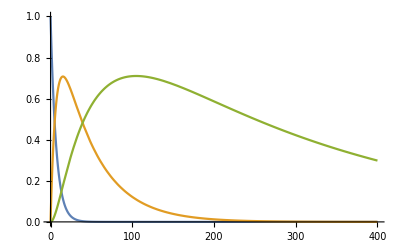

/Users/tomi/Dropbox (Cambridge University)/Physics/Fitting_Theory/Figures

./sequential_species/sola.csv

./sequential_species/solb.csv

./sequential_species/solc.csv

```mathematica
ClearAll[t0,t1,k11,k12,k13,k21,k22,k23,k31,k32,k33];

(* fitting period *) 
t0=0; 
t1=2*10^3; 

t0species = t0; 
t1species=t1;  

(* write out and solve our differential equation *) 
sol=ParametricNDSolveValue[{
D[a[t],t]==-k11*a[t]-k12*a[t]-k13*a[t],
a[t0] == 1,
D[b[t],t]==k11*a[t]+k12*a[t]+k13*a[t]-k21*b[t]-k22*b[t]-k23*b[t],
b[t0] == 0,
D[c[t],t]==k21*b[t]+k22*b[t]+k23*b[t]-k31 *c[t]-k32*c[t]-k33* c[t],
c[t0] == 0},
{a,b,c},{t,t0,t1},{k11,k12,k13,k21,k22,k23,k31,k32,k33}];

(* rate coefficients *)
rates = {k11-> 1/10,k12->1/30,k13-> 1/90,k21-> 1/90,k22-> 1/150,k23-> 1/200,k31-> 1/500,k32-> 1/1000,k33-> 1/2000};

(* select different components *) 
solutiona[t_]:= Module[{}, Return[(sol[k11,k12,k13,k21,k22,k23,k31,k32,k33]/.rates)[[1]][t]];
];
solutionb[t_]:= Module[{}, Return[(sol[k11,k12,k13,k21,k22,k23,k31,k32,k33]/.rates)[[2]][t]];
];
solutionc[t_]:= Module[{}, Return[(sol[k11,k12,k13,k21,k22,k23,k31,k32,k33]/.rates)[[3]][t]];
];

(* Plot the temporal components *) 
Plot[{solutiona[t],solutionb[t],solutionc[t]},{t,t0,t1/5},PlotRange->All]

sola = Table[{t,solutiona[t]},{t,t0,t1,0.1}];
solb = Table[{t,solutionb[t]},{t,t0,t1,0.1}];
solc = Table[{t,solutionc[t]},{t,t0,t1,0.1}];

SetDirectory[NotebookDirectory[]]

Export["./sequential_species/sola.csv",sola]
Export["./sequential_species/solb.csv",solb]
Export["./sequential_species/solc.csv",solc]
```

General::munfl: Exp[-2047.91] is too small to represent as a normalized machine number; precision may be lost.

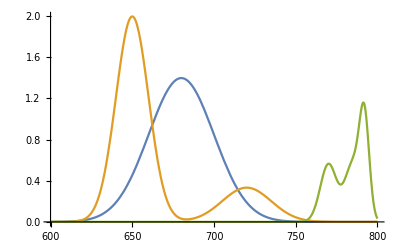

/Users/tomi/Dropbox (Cambridge University)/Physics/Fitting_Theory/Figures

General::munfl: Exp[-2048.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2026.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2005.56] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

./sequential_species/spectrum1.csv

./sequential_species/spectrum2.csv

./sequential_species/spectrum3.csv

```mathematica
(* define wavelength components *) 
spectrum1[w_] := Module[{v},
v= PDF[NormalDistribution[680,20]][w];
Return[70*v];
];
spectrum2[w_] := Module[{v}, 
v = PDF[NormalDistribution[650,10]][w]+1/4*PDF[NormalDistribution[720,15]][w]; 
Return[50*v];
];
spectrum3[w_] := Module[{v}, 
v = 1/2*PDF[NormalDistribution[785,5]][w]+1/2*PDF[NormalDistribution[792,3]][w]+1/2*PDF[NormalDistribution[770,5]][w]; 
Return[14*v];
];

(* Plot the spectrum *) 
Plot[{spectrum1[x],spectrum2[x],spectrum3[x]},{x,600,800},PlotRange->All]


SetDirectory[NotebookDirectory[]]

spec1 = Table[{x,N[spectrum1[x]]},{x,600,800,1}];
spec2 = Table[{x,N[spectrum2[x]]},{x,600,800,1}];
spec3 = Table[{x,N[spectrum3[x]]},{x,600,800,1}];

Export["./sequential_species/spectrum1.csv",spec1]
Export["./sequential_species/spectrum2.csv",spec2]
Export["./sequential_species/spectrum3.csv",spec3]
```

```mathematica
(* combine spectrum and time  *) 
combined[t_,w_]:= Module[{parta,partb,partc},
parta=spectrum1[w]*solutiona[t];
partb=spectrum2[w]*solutionb[t];
partc=spectrum3[w]*solutionc[t];
Return[parta+partb+partc];
]


(* random noise *) 
noise[]:= Module[{v}, 
v= RandomReal[]/5; 
Return[v];
]

(* generate data *) 
times = N[fSpace[t0+1,t1,200]]-1;
Quiet[data=Table[{t,w,combined[t,w]+noise[]},{t,times},{w,600,800,1}]];
data=Flatten[data,1];

(* have a look at the data *) 
ListDensityPlot[data,PlotRange->All,ScalingFunctions->{"Log","Linear","Linear"}];

speciesdata= data;


Export["./sequential_species/speciesdata.csv",Join[{{"X","Y","Z"}},speciesdata]];
```

```mathematica
Dimensions[times]
```

{200}

Generate Moving Dataset

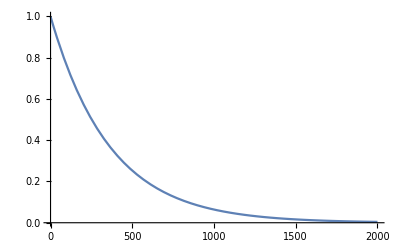

/Users/tomi/Dropbox (Cambridge University)/Physics/Fitting_Theory/Figures

./moving/sola.csv

```mathematica
ClearAll[t0,t1];

(* fitting period *) 
t0=0; 
t1=2*10^3; 

t0moving=t0; 
t1moving = t1; 

(* write out and solve our differential equation *) 
sol=ParametricNDSolveValue[{
D[a[t],t]==-k11*a[t]-k12*a[t]-k13*a[t],
a[t0] == 1},
{a,b,c},{t,t0,t1},{k11,k12,k13}];

(* rate coefficients *)
rates = {k11-> 1/2000,k12->1/800,k13-> 1/1000};

(* select different components *) 
solutiona[t_]:= Module[{}, Return[(sol[k11,k12,k13]/.rates)[[1]][t]];
];

(* Plot the temporal components *) 
Plot[{solutiona[t]},{t,t0,t1},PlotRange->All]


sola = Table[{t,solutiona[t]},{t,t0,t1,0.1}];

SetDirectory[NotebookDirectory[]]

Export["./moving/sola.csv",sola]
```

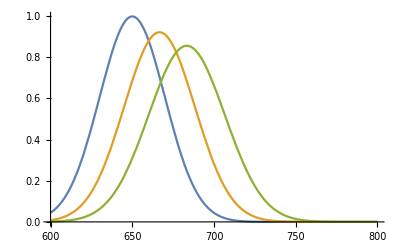

/Users/tomi/Dropbox (Cambridge University)/Physics/Fitting_Theory/Figures

./moving/spectrum1.csv

./moving/spectrum2.csv

./moving/spectrum3.csv

```mathematica
(* define wavelength components *) 
spectrum1[w_,t_] := Module[{v},
v= PDF[NormalDistribution[650+t/15,20+t/150]][w];
Return[50*v];
];

(* Plot the spectrum *) 
Plot[{spectrum1[x,t0],spectrum1[x,t0+250],spectrum1[x,t0+500]},{x,600,800},PlotRange->All]

SetDirectory[NotebookDirectory[]]

spec1 = Table[{x,N[spectrum1[x,t0]]},{x,600,800,1}];
spec2 = Table[{x,N[spectrum1[x,t0+250]]},{x,600,800,1}];
spec3 = Table[{x,N[spectrum1[x,t0+500]]},{x,600,800,1}];

Export["./moving/spectrum1.csv",spec1]
Export["./moving/spectrum2.csv",spec2]
Export["./moving/spectrum3.csv",spec3]
```

```mathematica
(* combine spectrum and time  *) 
combined[t_,w_]:= Module[{parta},
parta=spectrum1[w,t]*solutiona[t];
Return[parta];
]


(* random noise *) 
noise[]:= Module[{v}, 
v= RandomReal[]/10; 
Return[v];
]

(* generate data *) 
times = N[fSpace[t0+1,t1,200]]-1;
Quiet[data=Table[{t,w,combined[t,w]+noise[]},{t,times},{w,600,800,1}]];
data=Flatten[data,1];

(* have a look at the data *) 
ListDensityPlot[data,PlotRange->All,ScalingFunctions->{"Log","Linear","Linear"}]

movingdata = data; 


Export["./moving/movingdata.csv",Join[{{"X","Y","Z"}},movingdata]];
```

-Graphics-

Import Cell Dataset

```mathematica
(* Import Cell Dataset *) 

SetDirectory[NotebookDirectory[]];
files=FileNames["./cell_data/*wtf"];
importfiles= Import[#,"Data"]&/@files;

(* convert machine output into our useable dataset *) 
cells=datamould[importfiles[[1]]];

(* Convert DT/T data to OD *) 
cells[[;;,3]] = converttoOD[cells[[;;,3]]];

(* Interpolations from real data *) 
cellsint = Interpolation[cells,InterpolationOrder->1];
(* interpolations background corrected *) 
cellsint2[t_,w_]:=Module[{},result = cellsint[t,w]-Mean[cellsint[#,w]&/@{-2000,-3000,-4000,-5000}]];

(* export data *) 
wavelengths=Flatten[DeleteDuplicates[cells[[;;,{2}]]]];
times=Flatten[DeleteDuplicates[cells[[;;,{1}]]]];
celldata=Flatten[Table[{t,w,Re[cellsint2[t,w]]},{w,wavelengths},{t,times}],1];
(*Print["wavelengths"<>ToString[Length[wavelengths]]<>"times"<>ToString[Length[times]]] *) 
(* Export["./output/maps/celldata.csv",Join[{{"X","Y","Z"}},celldata]] *) 

Export["./celldata.csv",Join[{{"X","Y","Z"}},celldata]]
```

./celldata.csv

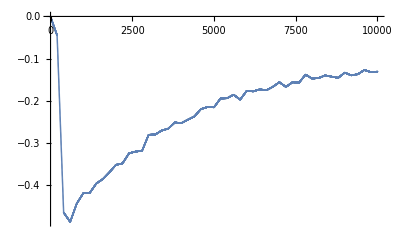

```mathematica
ListPlot[Table[Re[cellsint2[x,690]]*1000,{x,0,10000}]]
```

Import PSII Dataset

```mathematica
(* Import Cell Dataset *) 

SetDirectory[NotebookDirectory[]];
files=FileNames["./psii_data/*wtf"];
importfiles= Import[#,"Data"]&/@files;

(* convert machine output into our useable dataset *) 
psii=datamould[importfiles[[1]]];

(* Convert DT/T data to OD *) 
psii[[;;,3]] = converttoOD[psii[[;;,3]]];

(* Interpolations from real data *) 
psiiint = Interpolation[psii,InterpolationOrder->1];
(* interpolations background corrected *) 
psiiint2[t_,w_]:=Module[{},result = psiiint[t,w]-Mean[psiiint[#,w]&/@{-2000,-3000,-4000,-5000}]];

(* export data *) 
wavelengths=Flatten[DeleteDuplicates[psii[[;;,{2}]]]];
times=Flatten[DeleteDuplicates[psii[[;;,{1}]]]];
psiidata=Flatten[Table[{t,w,Re[psiiint2[t,w]]},{w,wavelengths},{t,times}],1];
(*Print["wavelengths"<>ToString[Length[wavelengths]]<>"times"<>ToString[Length[times]]] *) 
(* Export["./output/maps/celldata.csv",Join[{{"X","Y","Z"}},celldata]] *) 

Export["./psiidata.csv",Join[{{"X","Y","Z"}},psiidata]]
```

./psiidata.csv

```mathematica
Length[wavelengths]
Length[times]
```

245

179

```mathematica
ListPlot[Table[Re[cellsint2[x,690]]*1000,{x,0,10000}]]
```

-Graphics-

Import PSI Dataset

```mathematica
(* Import Cell Dataset *) 

SetDirectory[NotebookDirectory[]];
files=FileNames["./psi_data/*wtf"];
importfiles= Import[#,"Data"]&/@files;

(* convert machine output into our useable dataset *) 
psi=datamould[importfiles[[1]]];

(* Convert DT/T data to OD *) 
psi[[;;,3]] = converttoOD[psi[[;;,3]]];

(* Interpolations from real data *) 
psiint = Interpolation[psi,InterpolationOrder->1];
(* interpolations background corrected *) 
psiint2[t_,w_]:=Module[{},result = psiint[t,w]-Mean[psiint[#,w]&/@{-2000,-3000,-4000,-5000}]];

(* export data *) 
wavelengths=Flatten[DeleteDuplicates[psi[[;;,{2}]]]];
times=Flatten[DeleteDuplicates[psi[[;;,{1}]]]];
psidata=Flatten[Table[{t,w,Re[psiint2[t,w]]},{w,wavelengths},{t,times}],1];
(*Print["wavelengths"<>ToString[Length[wavelengths]]<>"times"<>ToString[Length[times]]] *) 
(* Export["./output/maps/celldata.csv",Join[{{"X","Y","Z"}},celldata]] *) 

Export["./psidata.csv",Join[{{"X","Y","Z"}},psidata]]
```

./psidata.csv

```mathematica
Length[wavelengths]
Length[times]
```

245

179

```mathematica
ListPlot[Table[Re[cellsint2[x,690]]*1000,{x,0,10000}]]
```

-Graphics-

Import Test Dataset from PyLDM

```mathematica
(* Import Cell Dataset *) 

SetDirectory[NotebookDirectory[]];
files=FileNames["./pyLDM/*csv"];
importfiles= Import[#,"Data"]&/@files;

testdataset=importfiles[[1]];
```

```mathematica
wavelengths=testdataset[[1,2;;]];
times = testdataset[[;;,1]];
data=testdataset[[2;;]];
data=data[[;;,2;;]];

t0ldm=times[[1]];
t1ldm=times[[-1]];

Dimensions[data];

data2= Table[{times[[t]],600+wavelengths[[w]]*0.66,data[[t,w]]},{t,1,100,1},{w,1,300,1}];

dataldm=Flatten[data2,1];
```

k1->k2->branch

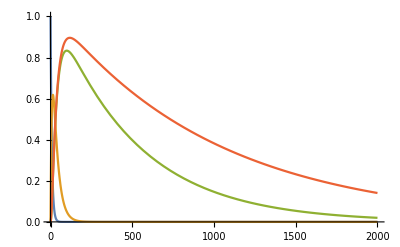

```mathematica
ClearAll[t0,t1];

(* fitting period *) 
t0=0; 
t1=2*10^3; 

t0branch = t0; 
t1branch=t1;  

(* write out and solve our differential equation *) 
sol=ParametricNDSolveValue[{
D[a[t],t]==-k11*a[t],
a[t0] == 1,
D[b[t],t]==k11*a[t]- 2*k21*b[t],
b[t0] == 0,
D[c[t],t]==k21*b[t]-k31 *c[t],
c[t0] == 0,
D[d[t],t]==k21*b[t]-k41 *d[t],
d[t0] == 0},
{a,b,c,d},{t,t0,t1},{k11,k21,k31,k41}];

(* rate coefficients *)
rates = {k11-> 1/8,k21-> 1/30,k31-> 1/500,k41-> 1/1000};

(* select different components *) 
solutiona[t_]:= Module[{}, Return[(sol[k11,k21,k31,k41]/.rates)[[1]][t]];
];
solutionb[t_]:= Module[{}, Return[(sol[k11,k21,k31,k41]/.rates)[[2]][t]];
];
solutionc[t_]:= Module[{}, Return[(sol[k11,k21,k31,k41]/.rates)[[3]][t]];
];
solutiond[t_]:= Module[{}, Return[(sol[k11,k21,k31,k41]/.rates)[[4]][t]];
];

(* Plot the temporal components *) 
Plot[{solutiona[t],solutionb[t],solutionc[t],solutiond[t]},{t,t0,t1},PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]]

speciesa =Table[{t,solutiona[t]},{t,t0,t1,1}];
speciesb =Table[{t,solutionb[t]},{t,t0,t1,1}];
speciesc =Table[{t,solutionc[t]},{t,t0,t1,1}];
speciesd =Table[{t,solutiond[t]},{t,t0,t1,1}];

Export["popbrancha.csv",speciesa]
Export["popbranchb.csv",speciesb]
Export["popbranchc.csv",speciesc]
Export["popbranchd.csv",speciesd]
```

/Users/tomi/Dropbox (Cambridge University)/Physics/Fitting_Theory/Figures

popbrancha.csv

popbranchb.csv

popbranchc.csv

popbranchd.csv

General::munfl: Exp[-2047.91] is too small to represent as a normalized machine number; precision may be lost.

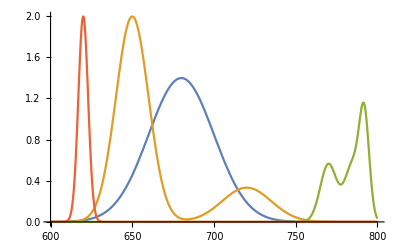

spectruma.csv

spectrumb.csv

General::munfl: Exp[-2048.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2026.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2005.56] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

spectrumc.csv

General::munfl: Exp[-709.389] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.12373×10^-308 0.398942 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

spectrumd.csv

```mathematica
(* define wavelength components *) 
spectrum1[w_] := Module[{v},
v= PDF[NormalDistribution[680,20]][w];
Return[70*v];
];
spectrum2[w_] := Module[{v}, 
v = PDF[NormalDistribution[650,10]][w]+1/4*PDF[NormalDistribution[720,15]][w]; 
Return[50*v];
];
spectrum3[w_] := Module[{v}, 
v = 1/2*PDF[NormalDistribution[785,5]][w]+1/2*PDF[NormalDistribution[792,3]][w]+1/2*PDF[NormalDistribution[770,5]][w]; 
Return[14*v];
];
spectrum4[w_] := Module[{v}, 
v = 1/2*PDF[NormalDistribution[620,3]][w]; 
Return[30*v];
];

(* Plot the spectrum *) 
Plot[{spectrum1[x],spectrum2[x],spectrum3[x],spectrum4[x]},{x,600,800},PlotRange->All]

spectruma =Table[{x,spectrum1[x]},{x,600,800,1}];
spectrumb =Table[{x,spectrum2[x]},{x,600,800,1}];
spectrumc =Table[{x,spectrum3[x]},{x,600,800,1}];
spectrumd =Table[{x,spectrum4[x]},{x,600,800,1}];

Export["spectruma.csv",N[spectruma]]
Export["spectrumb.csv",N[spectrumb]]
Export["spectrumc.csv",N[spectrumc]]
Export["spectrumd.csv",N[spectrumd]]
```

```mathematica
(* combine spectrum and time  *) 
combined[t_,w_]:= Module[{parta,partb,partc,partd},
parta=spectrum1[w]*solutiona[t];
partb=spectrum2[w]*solutionb[t];
partc=spectrum3[w]*solutionc[t];
partd=spectrum4[w]*solutiond[t];
Return[parta+partb+partc+partd];
]


(* random noise *) 
noise[]:= Module[{v}, 
v= RandomReal[]/10; 
Return[v];
]

(* generate data *) 
times = N[fSpace[t0+1,t1,100]]-1;
Quiet[data=Table[{t,w,combined[t,w]+noise[]},{t,times},{w,600,800,1}]];
data=Flatten[data,1];

(* have a look at the data *) 
ListDensityPlot[data,PlotRange->All,ScalingFunctions->{"Log","Linear","Linear"}];

branchdata= data;




Export["./branchdata.csv",Join[{{"X","Y","Z"}},branchdata]];
```

```mathematica
Dimensions[times]
Dimensions[times]
```

{100}

{100}

k1->k2->k3

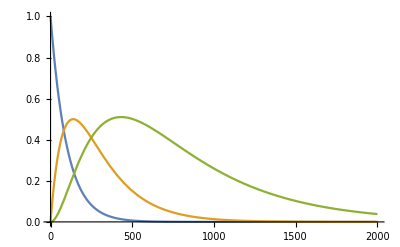

/Users/tomi/Dropbox (Cambridge University)/Physics/Fitting_Theory/Figures

./individual_species/sola.csv

./individual_species/solb.csv

./individual_species/solc.csv

```mathematica
ClearAll[t0,t1];

(* fitting period *) 
t0=0; 
t1=2*10^3; 

t0linear = t0; 
t1linear=t1;  

(* write out and solve our differential equation *) 
sol=ParametricNDSolveValue[{
D[a[t],t]==-k11*a[t],
a[t0] == 1,
D[b[t],t]==k11*a[t]-k21*b[t],
b[t0] == 0,
D[c[t],t]==k21*b[t] - k31*c[t],
c[t0] == 0},
{a,b,c},{t,t0,t1},{k11,k21,k31}];

(* rate coefficients *)
rates = {k11-> 1/100,k21-> 1/200,k31-> 1/500};

(* select different components *) 
solutiona[t_]:= Module[{}, Return[(sol[k11,k21,k31]/.rates)[[1]][t]];
];
solutionb[t_]:= Module[{}, Return[(sol[k11,k21,k31]/.rates)[[2]][t]];
];
solutionc[t_]:= Module[{}, Return[(sol[k11,k21,k31]/.rates)[[3]][t]];
];

(* Plot the temporal components *) 
Plot[{solutiona[t],solutionb[t],solutionc[t]},{t,t0,t1},PlotRange->All]

sola = Table[{t,solutiona[t]},{t,t0,t1,0.1}];
solb = Table[{t,solutionb[t]},{t,t0,t1,0.1}];
solc = Table[{t,solutionc[t]},{t,t0,t1,0.1}];

SetDirectory[NotebookDirectory[]]

Export["./individual_species/sola.csv",sola]
Export["./individual_species/solb.csv",solb]
Export["./individual_species/solc.csv",solc]
```

```mathematica
(* define wavelength components *) 
spectrum1[w_] := Module[{v},
v= PDF[NormalDistribution[680,20]][w];
Return[70*v];
];
spectrum2[w_] := Module[{v}, 
v = PDF[NormalDistribution[650,10]][w]+1/4*PDF[NormalDistribution[720,15]][w]; 
Return[50*v];
];
spectrum3[w_] := Module[{v}, 
v = 1/2*PDF[NormalDistribution[785,5]][w]+1/2*PDF[NormalDistribution[792,3]][w]+1/2*PDF[NormalDistribution[770,5]][w]; 
Return[14*v];
];

spec1 = Table[{x,N[spectrum1[x]]},{x,600,800,1}];
spec2 = Table[{x,N[spectrum2[x]]},{x,600,800,1}];
spec3 = Table[{x,N[spectrum3[x]]},{x,600,800,1}];

Export["./individual_species/spectrum1.csv",spec1]
Export["./individual_species/spectrum2.csv",spec2]
Export["./individual_species/spectrum3.csv",spec3]

(* Plot the spectrum *) 
Plot[{spectrum1[x],spectrum2[x],spectrum3[x]},{x,600,800},PlotRange->All]
```

General::munfl: Exp[-2048.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2026.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2005.56] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

./individual_species/spectrum1.csv

./individual_species/spectrum2.csv

./individual_species/spectrum3.csv

General::munfl: Exp[-2047.91] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

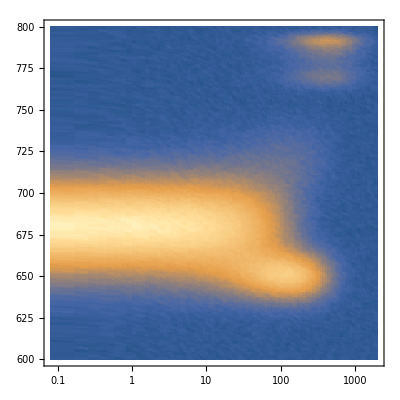

```mathematica
(* combine spectrum and time  *) 
combined[t_,w_]:= Module[{parta,partb,partc},
parta=spectrum1[w]*solutiona[t];
partb=spectrum2[w]*solutionb[t];
partc=spectrum3[w]*solutionc[t];
Return[parta+partb+partc];
]


(* random noise *) 
noise[]:= Module[{v}, 
v= RandomReal[]/10; 
Return[v];
]


(* generate data *) 
times = N[fSpace[t0+1,t1,100]]-1;
Quiet[data=Table[{t,w,combined[t,w]+noise[]},{t,times},{w,600,800,1}]];
data=Flatten[data,1];

(* have a look at the data *) 
ListDensityPlot[data,PlotRange->All,ScalingFunctions->{"Log","Linear","Linear"}]

lineardata= data;

Export["./individual_species/lineardata.csv",Join[{{"X","Y","Z"}},lineardata]];
```

k1->complicated

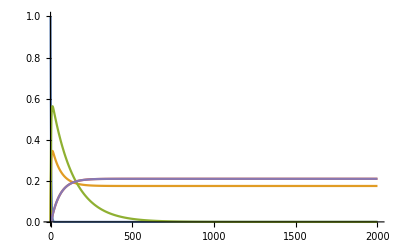

```mathematica
ClearAll[t0,t1];

(* fitting period *) 
t0=0; 
t1=2*10^3; 

t0complicated = t0; 
t1complicated=t1;  

(* write out and solve our differential equation *) 
sol=ParametricNDSolveValue[{
D[a[t],t]==-k11*a[t]-k12*a[t],
a[t0] == 1,
D[b[t],t]==k11*a[t]-k21*b[t]+k41*d[t],
b[t0] == 0,
D[c[t],t]==k12*a[t] - k31*c[t]-k32*c[t],
c[t0] == 0,
D[d[t],t]==k21*b[t]-k41*d[t],
d[t0] == 0,
D[e[t],t]==k32*c[t],
e[t0] == 0},
{a,b,c,d,e},{t,t0,t1},{k11,k12,k21,k31,k32,k41}];

(* rate coefficients *)
rates = {k11-> 1/8,k12-> 1/5,k21-> 1/100,k31-> 1/200,k32-> 1/400,k41-> 1/120};

(* select different components *) 
solutiona[t_]:= Module[{}, Return[(sol[k11,k12,k21,k31,k32,k41]/.rates)[[1]][t]];
];
solutionb[t_]:= Module[{}, Return[(sol[k11,k12,k21,k31,k32,k41]/.rates)[[2]][t]];
];
solutionc[t_]:= Module[{}, Return[(sol[k11,k12,k21,k31,k32,k41]/.rates)[[3]][t]];
];
solutiond[t_]:= Module[{}, Return[(sol[k11,k12,k21,k31,k32,k41]/.rates)[[4]][t]];
];
solutione[t_]:= Module[{}, Return[(sol[k11,k12,k21,k31,k32,k41]/.rates)[[4]][t]];
];

(* Plot the temporal components *) 
Plot[{solutiona[t],solutionb[t],solutionc[t],solutiond[t],solutione[t]},{t,t0,t1},PlotRange->All]
```

General::munfl: Exp[-2047.91] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1422.15] is too small to represent as a normalized machine number; precision may be lost.

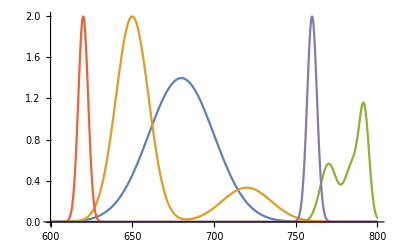

```mathematica
(* define wavelength components *) 
spectrum1[w_] := Module[{v},
v= PDF[NormalDistribution[680,20]][w];
Return[70*v];
];
spectrum2[w_] := Module[{v}, 
v = PDF[NormalDistribution[650,10]][w]+1/4*PDF[NormalDistribution[720,15]][w]; 
Return[50*v];
];
spectrum3[w_] := Module[{v}, 
v = 1/2*PDF[NormalDistribution[785,5]][w]+1/2*PDF[NormalDistribution[792,3]][w]+1/2*PDF[NormalDistribution[770,5]][w]; 
Return[14*v];
];
spectrum4[w_] := Module[{v}, 
v = 1/2*PDF[NormalDistribution[620,3]][w]; 
Return[30*v];
];

spectrum5[w_] := Module[{v}, 
v = 1/2*PDF[NormalDistribution[760,3]][w]; 
Return[30*v];
];

(* Plot the spectrum *) 
Plot[{spectrum1[x],spectrum2[x],spectrum3[x],spectrum4[x],spectrum5[x]},{x,600,800},PlotRange->All]
```

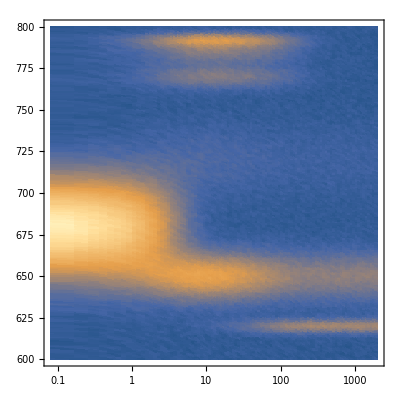

```mathematica
(* combine spectrum and time  *) 
combined[t_,w_]:= Module[{parta,partb,partc,partd,parte},
parta=spectrum1[w]*solutiona[t];
partb=spectrum2[w]*solutionb[t];
partc=spectrum3[w]*solutionc[t];
partd=spectrum4[w]*solutiond[t];
parte=spectrum4[w]*solutione[t];
Return[parta+partb+partc+partd];
]


(* random noise *) 
noise[]:= Module[{v}, 
v= RandomReal[]/10; 
Return[v];
]

(* generate data *) 
times = N[fSpace[t0+1,t1,100]]-1;
Quiet[data=Table[{t,w,combined[t,w]+noise[]},{t,times},{w,600,800,1}]];
data=Flatten[data,1];

(* have a look at the data *) 
ListDensityPlot[data,PlotRange->All,ScalingFunctions->{"Log","Linear","Linear"}]

complicateddata= data;
```

## SVD & GA Functions

```mathematica
(* selects a wavelength and time range *) 
selectdata[dataset_,wavelengthlow_,wavelengthhigh_,timelow_,timehigh_,flip_:1] := Module[{wavelengthclosestlow,wavelengthclosesthigh,timeclosestlow,timeclosesthigh,selection,ntimes,nwavelengths,times,wavelengths,check}, 

(* find wavelength closest to user input values *) 
wavelengthclosestlow = Nearest[dataset[[;;,2]],wavelengthlow][[1]];
wavelengthclosesthigh= Nearest[dataset[[;;,2]],wavelengthhigh][[1]];

(* make the selection *) 
selection=Select[dataset,wavelengthclosesthigh≥ #[[2]]≥ wavelengthclosestlow&];

(* find wavelength closest to user input values *) 
timeclosestlow = Nearest[selection[[;;,1]],timelow][[1]];
timeclosesthigh= Nearest[selection[[;;,1]],timehigh][[1]];

(* make the selection *) 
selection=Select[selection,timeclosesthigh≥ #[[1]]≥ timeclosestlow&];


(* Counbt number of distinct wavelengths and time steps  *) 
ntimes = CountDistinct[selection[[;;,{1}]]];
nwavelengths = CountDistinct[selection[[;;,{2}]]];

(* Record the steps of wavelengths and time steps  *) 
times = DeleteDuplicates[selection[[;;,{1}]]];
wavelengths=DeleteDuplicates[selection[[;;,{2}]]];

(* only take dOD data *) 
selection = Flatten[selection[[;;,{3}]]];

(* reshape to be appropraite for SVD analysis, x being wavlength and y being time *) 
check=flip;
If[check===1, 
selection= Transpose[ArrayReshape[selection,{nwavelengths,ntimes}]];,
selection= ArrayReshape[selection,{ntimes,nwavelengths}];
];


Return[{selection,ntimes,nwavelengths,times,wavelengths}]; 
]

(* SVD *) 
svd[data_]:= Module[{matrixU,matrixS,matrixVtranspose,wLSV,svdmatrices},

(* m is the number of time delays *) 
(* n is the spectral dependence - number of wavelengths *) 
(* m*m singular vectors giving the temporal dependance *) 

(* take SVD *) 
svdmatrices = SingularValueDecomposition[data];
matrixU =svdmatrices[[1]];
(* m*n is the diagonal matrix of singular values *) 
matrixS = svdmatrices[[2]];
(* Vt is the n*n unitary matrix giving the spectral dependence of the signal *) 
matrixVtranspose = svdmatrices[[3]];
(* weight left singular values .*) 
wLSV = matrixU.matrixS;

Return[{matrixU,matrixS,wLSV,matrixVtranspose}];
]

(* generate design matrix *) 
generateD[times_,taus_]:=Block[{matrixD,timesnum,i,j,numtau},
timesnum=Length[times]; 
numtau=Length[taus];
matrixD = Quiet[Table[SetPrecision[Exp[-times[[i]]/taus[[j]]],10],{i,1,timesnum,1},{j,1,numtau,1}]];
matrixD=Flatten[#]&/@matrixD;
Return[matrixD];
];

Clear[tominimize]
tominimize[taus_?(VectorQ[#,NumericQ]&),matrixY_,times_]:=Block[{matrixD,matrixDAS,residue}, 
matrixD = generateD[times,taus];
matrixDAS=LeastSquares[matrixD,matrixY];
residue = Total[(matrixY - matrixD.matrixDAS)^2,2];
Return[residue];
]

convertdata[data_,wavelengths_,times_]:= Module[{datahold,newdata}, 
(* add in wavelengths *) 
datahold =Transpose[{wavelengths,data[[#]]}]&/@Range[Length[data]];
(* add in times *) 
newdata =Table[Flatten/@Transpose[{times,Flatten[datahold[[;;,{i}]],1]}],{i,1,Dimensions[datahold][[2]],1}];
newdata =Flatten[newdata,1];
Return[newdata]; 
]
```

SVD and GA for k1->k2->k3 Dataset

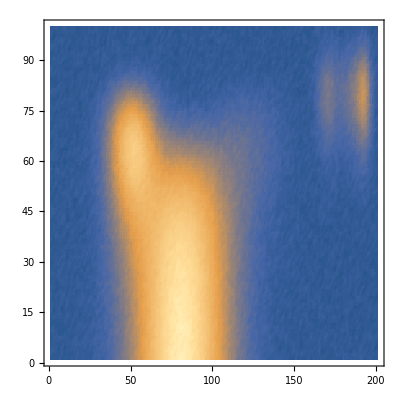

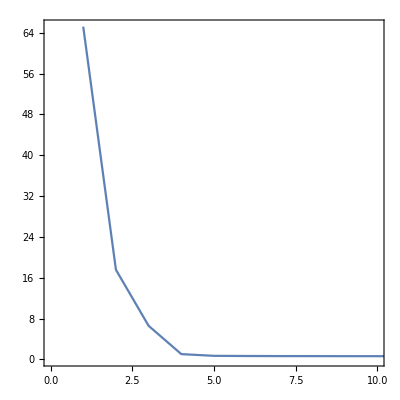

Part::partd: Part specification basis⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: basis⟦1⟧ is not a list of numbers or pairs of numbers.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[wavelengths].

Transpose::nmtx: The first two levels of {{600.,650.,700.,750.},{-571.082,-571.028,-570.98,-570.933,-570.895,-570.871,-570.86,-570.86,-570.867,-570.882,«634»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{600.,650.,700.,750.},{-571.082,-571.028,-570.98,-570.933,-570.895,-570.871,-570.86,-570.86,-570.867,-570.882,«634»}}] is not a list of numbers or pairs of numbers.

ListPlot::lpn: Transpose[{{-30.,-29.5,-29.,-28.5,-28.,-27.5,-27.,-26.5,-26.,-25.5,«151»},{-0.998649,-2.68271×10^-6,-0.0519592}}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{600.,650.,700.,750.},{-571.082,-571.028,-570.98,-570.933,-570.895,-570.871,-570.86,-570.86,-570.867,-570.882,«634»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{600.,650.,700.,750.},{-571.082,-571.028,-570.98,-570.933,-570.895,-570.871,-570.86,-570.86,-570.867,-570.882,«634»}}] is not a list of numbers or pairs of numbers.

ListPlot::lpn: Transpose[{{-30.,-29.5,-29.,-28.5,-28.,-27.5,-27.,-26.5,-26.,-25.5,«151»},{-0.998649,-2.68271×10^-6,-0.0519592}}] is not a list of numbers or pairs of numbers.

```mathematica
(* ----- SVD Analysis ---- *)  
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ lineardata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0species(* time to start fitting fs*), t1species (* time to end fitting (fs) *) ,"No Flip"];

(* take SVD decomposition to investigate which bases to keep *) 
{matrixU,matrixS,wLSV,matrixV} = svd[data];

(* time and wavelength reduced dataset *) 
ListDensityPlot[data,PlotRange->All]

numberofbasis = 10; (* must be less than dimensions of x *) 
basis=Transpose[{Flatten[times],Flatten[wLSV[[;;,{#}]]]}]&/@ Range[numberofbasis];

Manipulate[GraphicsRow[{ListPlot[basis[[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Time [fs]","wLSV "<>ToString[i]}}],ListPlot[Transpose[{Flatten[wavelengths],Transpose[matrixV][[i]]}],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Wavelength","wLSV "<>ToString[i]}}]}],{i,1,numberofbasis,1}]

(* Inspect Singular Values *) 
ListPlot[Select[Flatten[matrixS],#>0&],PlotRange->{{0,10},{0,All}},Joined->True,AspectRatio->1,Frame->True]
```

```mathematica
Export["./individual_species/singular_values.csv",Table[{i,Select[Flatten[matrixS],#>0&][[i]]},{i,1,Length[Select[Flatten[matrixS],#>0&]],1}]]
Table[Export["./individual_species/time_"<>ToString[i]<>".csv",basis[[i]]],{i,1,10,1}];
Table[Export["./individual_species/spectrum_"<>ToString[i]<>".csv",Transpose[{Flatten[wavelengths],Transpose[matrixV][[i]]}]],{i,1,10,1}];
```

```mathematica
(* ------ Global Analysis ------ *) 

(* Select which vectors you wish to keep - lets take 3 *) 
selectedvectors = {1,2,3};
wLSVreduced = wLSV[[;;,selectedvectors]];

(* lets guess our rates - must match number of wLSV*) 
taus = {100,200,300};
limits = {{5,5000},{1,1000},{1,1000}};

(* you must give the same number of taus as selectedvectors *) 
If[Length[taus]==Length[selectedvectors],
, 
MessageDialog["You have an incompatible number of lifetimes to vectors"]
Interrupt[];
]
 
(* limits of lifetimes *) 
variables=Table[t[i],{i,Length[taus]}];
f[{min_,max_},{pos_}]:=min<t[pos]<max
region=And@@MapIndexed[f,limits];

(* generate D *) 
matrixD = generateD[Flatten[times],taus];

(* generate Decay Associated Spectra *) 
matrixDAS=LeastSquares[matrixD,wLSVreduced];

(* run minimisation algorithim *) 
nmresults=NMinimize[{tominimize[variables,wLSVreduced,times],region},variables,PrecisionGoal->10,Method->"SimulatedAnnealing"]
```

{0.870745,{t[1]→824.073,t[2]→131.779,t[3]→131.778}}

```mathematica
(* ----- What Method is Fastest? ----- *)
```

```mathematica
Timing[NMinimize[{tominimize[variables,wLSVreduced,times],region},variables,PrecisionGoal->10,Method->"SimulatedAnnealing"]]
Timing[NMinimize[{tominimize[variables,wLSVreduced,times],region},variables,PrecisionGoal->10,Method->"RandomSearch"]]
Timing[NMinimize[{tominimize[variables,wLSVreduced,times],region},variables,PrecisionGoal->10,Method->"DifferentialEvolution"]]
Timing[NMinimize[{tominimize[variables,wLSVreduced,times],region},variables,PrecisionGoal->10,Method->"NelderMead"]]
```

```mathematica
ListPlot[Transpose[wLSVreduced]]
```

```mathematica
matrixDAS
```

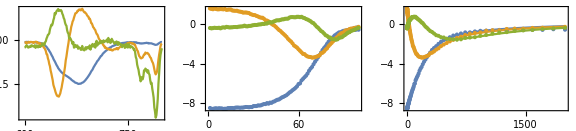

-Graphics-

```mathematica
(* ----- Global Analysis Results ------- *) 
tausfit = {variables}/.nmresults[[2]];
matrixD = generateD[Flatten[times],tausfit];
matrixDAS=LeastSquares[matrixD,wLSVreduced];

(* Plot Spectra  *)
spectra =Transpose[{Flatten[wavelengths],#}]&/@Transpose[matrixV[[;;,selectedvectors]]];
plot0=ListPlot[spectra,Joined->True,Frame->True];

(* Plot Temporal *) 
fit = Transpose[{Flatten[times],#}]&/@Transpose[matrixD.matrixDAS]; 
ogdata = Transpose[{Flatten[times],#}]&/@Transpose[wLSVreduced];
plot1=Show[ListPlot[Transpose[matrixD.matrixDAS],Joined->True,Frame->True,FrameLabel-> {"Data Points"," "}],ListPlot[Transpose[wLSVreduced],PlotRange->All]];
plot2=Show[ListPlot[fit,Joined->True,PlotRange->{{t0species,t1species},All},Frame->True,FrameLabel-> {"Time"," "}],ListPlot[ogdata,PlotRange->{{t0species,t1species},All}]];

GraphicsRow[{plot0,plot1,plot2},ImageSize->Large]


plot1=Show[ListPlot3D[{data,matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]},PlotRange->All]];
residues = Abs[data-matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]];
plot2=ListPlot3D[residues,PlotRange-> All];

GraphicsRow[{plot1,plot2},ImageSize->Large]
```

```mathematica
datatoplot = Transpose[{Flatten[wavelengths],data[[#]]}]&/@Range[Length[data]];
datatoplot=Flatten[Table[Flatten[#,1]&/@Transpose[{Flatten[times],datatoplot[[;;,i]]}],{i,1,201,1}],1];
datatoplot[[;;,{1,2}]]=datatoplot[[;;,{2,1}]];

fitdata = matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]];
fitdata = Transpose[{Flatten[wavelengths],fitdata[[#]]}]&/@Range[Length[fitdata]];
fitdata=Flatten[Table[Flatten[#,1]&/@Transpose[{Flatten[times],fitdata[[;;,i]]}],{i,1,201,1}],1];
fitdata[[;;,{1,2}]]=fitdata[[;;,{2,1}]];

residuesdata = residues;
residuesdata = Transpose[{Flatten[wavelengths],residuesdata[[#]]}]&/@Range[Length[residuesdata]];
residuesdata=Flatten[Table[Flatten[#,1]&/@Transpose[{Flatten[times],residuesdata[[;;,i]]}],{i,1,201,1}],1];
residuesdata[[;;,{1,2}]]=residuesdata[[;;,{2,1}]];
```

```mathematica
Export["./individual_species/residuesdata.csv",Join[{{"X","Y","Z"}},residuesdata]]
```

./individual_species/residuesdata.csv

Set::partd: Part specification datatoplot⟦1;;All,{1,2}⟧ is longer than depth of object.

```mathematica
datatoplot[[-1]]
```

{699,1999.,0.00113278}

```mathematica
plot=ListPlot3D[{datatoplot,fitdata},PlotRange->All,LabelStyle->{FontSize->16,FontFamily->"Arial",Black},Boxed->{Left,Bottom,Back},BoxStyle->Directive[Black,Thickness[0.003]] ,PlotLegends->{"Data","Fit"},AxesLabel->{" "," "," "},PlotRange->All,ImageSize->Large,PlotStyle->{{Opacity[0.5],Orange},{Opacity[0.8],LightBlue}},BoxRatios->{1,1,1},ViewAngle -> 0.5011114127587017, ViewPoint -> {1.6394402020656536, -1.921163927391434, 2.2519691356545835}, 
  ViewVertical -> {-0.4320076078992178, 0.5062444068462598, 0.7463819580175248},ScalingFunctions->{Identity,"Log",Identity}
]

(*Export["/Users/tomi/Downloads/map.pdf",plot,"PDF"]*)
```

-Graphics3D-

```mathematica
Export["./individual_species/SVDspectra.csv",{spectra[[1,;;,1]],spectra[[1,;;,2]],spectra[[2,;;,2]],spectra[[3,;;,2]]}];
Export["./individual_species/data.csv",{ogdata[[1,;;,1]],ogdata[[1,;;,2]],ogdata[[2,;;,2]],ogdata[[3,;;,2]]}];
Export["./individual_species/fit.csv",{fit[[1,;;,1]],fit[[1,;;,2]],fit[[2,;;,2]],fit[[3,;;,2]]}];
```

SVD and GA for Moving Species Dataset

```mathematica
(* ----- SVD Analysis ---- *)  
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ movingdata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0moving(* time to start fitting fs*), t1moving (* time to end fitting (fs) *) ,"No Flip"];

(* take SVD decomposition to investigate which bases to keep *) 
{matrixU,matrixS,wLSV,matrixV} = svd[data];

(* time and wavelength reduced dataset *) 
ListDensityPlot[data,PlotRange->All]

numberofbasis = 10; (* must be less than dimensions of x *) 
basis=Transpose[{Flatten[times],Flatten[wLSV[[;;,{#}]]]}]&/@ Range[numberofbasis];

Manipulate[GraphicsRow[{ListPlot[basis[[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Time [fs]","wLSV "<>ToString[i]}}],ListPlot[Transpose[matrixV][[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Wavelength","wLSV "<>ToString[i]}}]}],{i,1,numberofbasis,1}]
```

```mathematica
Export["./moving/singular_values.csv",Table[{i,Select[Flatten[matrixS],#>0&][[i]]},{i,1,Length[Select[Flatten[matrixS],#>0&]],1}]]
Table[Export["./moving/time_"<>ToString[i]<>".csv",basis[[i]]],{i,1,10,1}];
Table[Export["./moving/spectrum_"<>ToString[i]<>".csv",Transpose[{Flatten[wavelengths],Transpose[matrixV][[i]]}]],{i,1,10,1}];
```

SVD and GA for pyLDM Dataset

```mathematica
(* ----- SVD Analysis ---- *)  
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ dataldm (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0ldm(* time to start fitting fs*), t1ldm (* time to end fitting (fs) *) ,"No Flip"];

(* take SVD decomposition to investigate which bases to keep *) 
{matrixU,matrixS,wLSV,matrixV} = svd[data];

(* time and wavelength reduced dataset *) 
ListDensityPlot[data,PlotRange->All]

numberofbasis = 10; (* must be less than dimensions of x *) 
basis=Transpose[{Flatten[times],Flatten[wLSV[[;;,{#}]]]}]&/@ Range[numberofbasis];

Manipulate[GraphicsRow[{ListPlot[basis[[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Time [fs]","wLSV "<>ToString[i]}}],ListPlot[Transpose[matrixV][[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Wavelength","wLSV "<>ToString[i]}}]}],{i,1,numberofbasis,1}]
```

```mathematica
(* Inspect Singular Values *) 
ListPlot[Select[Flatten[matrixS],#>0&],PlotRange->{{0,10},{0,200}},Joined->True,AspectRatio->1,Frame->True]
```

SVD and GA for Cell Dataset

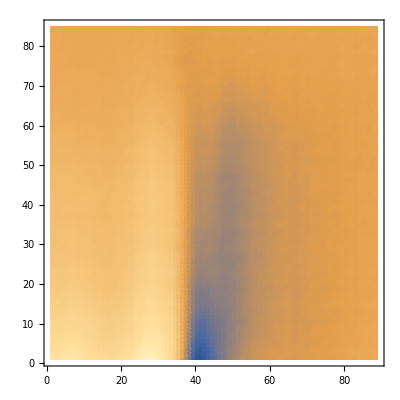

```mathematica
(* ----- SVD Analysis ---- *)  
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[  celldata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,750(* time to start fitting fs*), 100000 (* time to end fitting (fs) *) ,1];

(* take SVD decomposition to investigate which bases to keep *) 
{matrixU,matrixS,wLSV,matrixV} = svd[data];

(* time and wavelength reduced dataset *) 
ListDensityPlot[data,PlotRange->All]

numberofbasis = 4; (* must be less than dimensions of x *) 
basis=Transpose[{Flatten[times],Flatten[wLSV[[;;,{#}]]]}]&/@ Range[numberofbasis];

Manipulate[GraphicsRow[{ListPlot[basis[[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Time [fs]","wLSV "<>ToString[i]}}],ListPlot[Transpose[matrixV][[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Wavelength","wLSV "<>ToString[i]}}]}],{i,1,numberofbasis,1}]
```

```mathematica
Export["./cell/singular_values.csv",Table[{i,Select[Flatten[matrixS],#>0&][[i]]},{i,1,Length[Select[Flatten[matrixS],#>0&]],1}]]
Table[Export["./cell/time_"<>ToString[i]<>".csv",basis[[i]]],{i,1,10,1}];
Table[Export["./cell/spectrum_"<>ToString[i]<>".csv",Transpose[{Flatten[wavelengths],Transpose[matrixV][[i]]}]],{i,1,10,1}];
```

```mathematica
(* Select which vectors you wish to keep - lets take 3 *) 
selectedvectors = {1,2,3,4};
wLSVreduced = wLSV[[;;,selectedvectors]];

(* lets guess our rates - must match number of wLSV*) 
taus = {100,200,300,400};
limits = {{5,50000},{1,10000},{1,100000},{1,100000}};

(* you must give the same number of taus as selectedvectors *) 
If[Length[taus]==Length[selectedvectors],
, 
MessageDialog["You have an incompatible number of lifetimes to vectors"]
Interrupt[];
]
 
(* limits of lifetimes *) 
variables=Table[t[i],{i,Length[taus]}];
f[{min_,max_},{pos_}]:=min<t[pos]<max
region=And@@MapIndexed[f,limits];

(* generate D *) 
matrixD = generateD[Flatten[times],taus];

(* generate Decay Associated Spectra *) 
matrixDAS=LeastSquares[matrixD,wLSVreduced];

(* run minimisation algorithim *) 
nmresults=NMinimize[{tominimize[variables,wLSVreduced,times],region},variables,PrecisionGoal->10,Method->"SimulatedAnnealing"]
```

{8.56325×10^-8,{t[1]→19857.5,t[2]→3450.24,t[3]→15840.3,t[4]→86978.4}}

```mathematica
(* ----- Global Analysis Results ------- *) 
tausfit = {variables}/.nmresults[[2]];
matrixD = generateD[Flatten[times],tausfit];
matrixDAS=LeastSquares[matrixD,wLSVreduced];

(* Plot Spectra  *)
spectra =Transpose[{Flatten[wavelengths],#}]&/@Transpose[matrixV[[;;,selectedvectors]]];
plot0=ListPlot[spectra,Joined->True,Frame->True];

(* Plot Temporal *) 
fit = Transpose[{Flatten[times],#}]&/@Transpose[matrixD.matrixDAS]; 
ogdata = Transpose[{Flatten[times],#}]&/@Transpose[wLSVreduced];
plot1=Show[ListPlot[Transpose[matrixD.matrixDAS],Joined->True,Frame->True,FrameLabel-> {"Data Points"," "}],ListPlot[Transpose[wLSVreduced],PlotRange->All]];
plot2=Show[ListPlot[fit,Joined->True,PlotRange->{{t0species,t1species},All},Frame->True,FrameLabel-> {"Time"," "}],ListPlot[ogdata,PlotRange->{{t0species,t1species},All}]];

GraphicsRow[{plot0,plot1,plot2},ImageSize->Large]


plot1=Show[ListPlot3D[{data,matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]},PlotRange->All]];
residues = Abs[data-matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]];
plot2=ListPlot3D[residues,PlotRange-> All];

GraphicsRow[{plot1,plot2},ImageSize->Large]
```

```mathematica
(* Inspect Singular Values *) 
ListPlot[Select[Flatten[matrixS],#>0&],PlotRange->{{0,10},{0,All}},Joined->True,AspectRatio->1,Frame->True]
```

SVD and GA for PSI Dataset

```mathematica
(* ----- SVD Analysis ---- *)  
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ psidata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,700(* time to start fitting fs*), 100000 (* time to end fitting (fs) *) ,1];

(* take SVD decomposition to investigate which bases to keep *) 
{matrixU,matrixS,wLSV,matrixV} = svd[data];

(* time and wavelength reduced dataset *) 
ListDensityPlot[data,PlotRange->All]

numberofbasis = 10; (* must be less than dimensions of x *) 
basis=Transpose[{Flatten[times],Flatten[wLSV[[;;,{#}]]]}]&/@ Range[numberofbasis];

Manipulate[GraphicsRow[{ListPlot[basis[[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Time [fs]","wLSV "<>ToString[i]}}],ListPlot[Transpose[matrixV][[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Wavelength","wLSV "<>ToString[i]}}]}],{i,1,numberofbasis,1}]
```

```mathematica
Export["./psi/singular_values.csv",Table[{i,Select[Flatten[matrixS],#>0&][[i]]},{i,1,Length[Select[Flatten[matrixS],#>0&]],1}]]
Table[Export["./psi/time_"<>ToString[i]<>".csv",basis[[i]]],{i,1,10,1}];
Table[Export["./psi/spectrum_"<>ToString[i]<>".csv",Transpose[{Flatten[wavelengths],Transpose[matrixV][[i]]}]],{i,1,10,1}];
```

```mathematica
(* Inspect Singular Values *) 
ListPlot[Select[Flatten[matrixS],#>0&],PlotRange->{{0,10},{0,All}},Joined->True,AspectRatio->1,Frame->True]
```

SVD and GA for PSI Dataset

```mathematica
(* ----- SVD Analysis ---- *)  
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ psiidata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,700(* time to start fitting fs*), 100000 (* time to end fitting (fs) *) ,1];

(* take SVD decomposition to investigate which bases to keep *) 
{matrixU,matrixS,wLSV,matrixV} = svd[data];

(* time and wavelength reduced dataset *) 
ListDensityPlot[data,PlotRange->All]

numberofbasis = 10; (* must be less than dimensions of x *) 
basis=Transpose[{Flatten[times],Flatten[wLSV[[;;,{#}]]]}]&/@ Range[numberofbasis];

Manipulate[GraphicsRow[{ListPlot[basis[[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Time [fs]","wLSV "<>ToString[i]}}],ListPlot[Transpose[matrixV][[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Wavelength","wLSV "<>ToString[i]}}]}],{i,1,numberofbasis,1}]
```

```mathematica
Export["./psii/singular_values.csv",Table[{i,Select[Flatten[matrixS],#>0&][[i]]},{i,1,Length[Select[Flatten[matrixS],#>0&]],1}]]
Table[Export["./psii/time_"<>ToString[i]<>".csv",basis[[i]]],{i,1,10,1}];
Table[Export["./psii/spectrum_"<>ToString[i]<>".csv",Transpose[{Flatten[wavelengths],Transpose[matrixV][[i]]}]],{i,1,10,1}];
```

```mathematica
(* Inspect Singular Values *) 
ListPlot[Select[Flatten[matrixS],#>0&],PlotRange->{{0,10},{0,All}},Joined->True,AspectRatio->1,Frame->True]
```

SVD and GA for Branch Dataset

```mathematica
(* ----- SVD Analysis ---- *)  
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ branchdata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0branch(* time to start fitting fs*), t1branch (* time to end fitting (fs) *) ,"No Flip"];

(* take SVD decomposition to investigate which bases to keep *) 
{matrixU,matrixS,wLSV,matrixV} = svd[data];

(* time and wavelength reduced dataset *) 
ListDensityPlot[data,PlotRange->All]

numberofbasis = 10; (* must be less than dimensions of x *) 
basis=Transpose[{Flatten[times],Flatten[wLSV[[;;,{#}]]]}]&/@ Range[numberofbasis];

Manipulate[GraphicsRow[{ListPlot[basis[[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Time [fs]","wLSV "<>ToString[i]}}],ListPlot[Transpose[matrixV][[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Wavelength","wLSV "<>ToString[i]}}]}],{i,1,numberofbasis,1}]
```

```mathematica
Export["./branch/singular_values.csv",Table[{i,Select[Flatten[matrixS],#>0&][[i]]},{i,1,Length[Select[Flatten[matrixS],#>0&]],1}]]
Table[Export["./branch/time_"<>ToString[i]<>".csv",basis[[i]]],{i,1,10,1}];
Table[Export["./branch/spectrum_"<>ToString[i]<>".csv",Transpose[{Flatten[wavelengths],Transpose[matrixV][[i]]}]],{i,1,10,1}];
```

## LDA Functions

```mathematica
(* selects a wavelength and time range *) 
selectdata[dataset_,wavelengthlow_,wavelengthhigh_,timelow_,timehigh_,flip_:1] := Module[{wavelengthclosestlow,wavelengthclosesthigh,timeclosestlow,timeclosesthigh,selection,ntimes,nwavelengths,times,wavelengths,check}, 

(* find wavelength closest to user input values *) 
wavelengthclosestlow = Nearest[dataset[[;;,2]],wavelengthlow][[1]];
wavelengthclosesthigh= Nearest[dataset[[;;,2]],wavelengthhigh][[1]];

(* make the selection *) 
selection=Select[dataset,wavelengthclosesthigh≥ #[[2]]≥ wavelengthclosestlow&];

(* find wavelength closest to user input values *) 
timeclosestlow = Nearest[selection[[;;,1]],timelow][[1]];
timeclosesthigh= Nearest[selection[[;;,1]],timehigh][[1]];

(* make the selection *) 
selection=Select[selection,timeclosesthigh≥ #[[1]]≥ timeclosestlow&];


(* Counbt number of distinct wavelengths and time steps  *) 
ntimes = CountDistinct[selection[[;;,{1}]]];
nwavelengths = CountDistinct[selection[[;;,{2}]]];

(* Record the steps of wavelengths and time steps  *) 
times = DeleteDuplicates[selection[[;;,{1}]]];
wavelengths=DeleteDuplicates[selection[[;;,{2}]]];

(* only take dOD data *) 
selection = Flatten[selection[[;;,{3}]]];

(* reshape to be appropraite for SVD analysis, x being wavlength and y being time *) 
check=flip;
If[check===1, 
selection= Transpose[ArrayReshape[selection,{nwavelengths,ntimes}]];,
selection= ArrayReshape[selection,{ntimes,nwavelengths}];
];


Return[{selection,ntimes,nwavelengths,times,wavelengths}]; 
]

(* SVD *) 
svd[data_]:= Module[{matrixU,matrixS,matrixVtranspose,wLSV,svdmatrices},

(* m is the number of time delays *) 
(* n is the spectral dependence - number of wavelengths *) 
(* m*m singular vectors giving the temporal dependance *) 

(* take SVD *) 
svdmatrices = SingularValueDecomposition[data];
matrixU =svdmatrices[[1]];
(* m*n is the diagonal matrix of singular values *) 
matrixS = svdmatrices[[2]];
(* Vt is the n*n unitary matrix giving the spectral dependence of the signal *) 
matrixVtranspose = svdmatrices[[3]];
(* weight left singular values .*) 
wLSV = matrixU.matrixS;

Return[{matrixU,matrixS,wLSV,matrixVtranspose}];
]

(* generate design matrix *) 
generateD[times_,taus_]:=Block[{matrixD,timesnum,i,j,numtau},
timesnum=Length[times]; 
numtau=Length[taus];
matrixD = Quiet[Table[SetPrecision[Exp[-times[[i]]/taus[[j]]],10],{i,1,timesnum,1},{j,1,numtau,1}]];
matrixD=Flatten[#]&/@matrixD;
Return[matrixD];
];

Clear[tominimize]
tominimize[taus_?(VectorQ[#,NumericQ]&),matrixY_,times_]:=Block[{matrixD,matrixDAS,residue}, 
matrixD = generateD[times,taus];
matrixDAS=LeastSquares[matrixD,matrixY];
residue = Total[(matrixY - matrixD.matrixDAS)^2,2];
Return[residue];
]

convertdata[data_,wavelengths_,times_]:= Module[{datahold,newdata}, 
(* add in wavelengths *) 
datahold =Transpose[{wavelengths,data[[#]]}]&/@Range[Length[data]];
(* add in times *) 
newdata =Table[Flatten/@Transpose[{times,Flatten[datahold[[;;,{i}]],1]}],{i,1,Dimensions[datahold][[2]],1}];
newdata =Flatten[newdata,1];
Return[newdata]; 
]
```

LDA for linear Dataset

```mathematica
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ lineardata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0linear(* time to start fitting fs*), t1linear (* time to end fitting (fs) *) ,"No Flip"];

(* Set order magnitude range of Taus *) 
mintau =1;
maxtau = 4;
numtaus = 1000; 

(* Set order magnitude range over regularisation coefficients *) 
alphamin =0.1; 
alphamax = 1; 
numalphas = 10; 

(* give minimum and maximum taus, with number of taus *) 
logtaus = logspace[mintau,maxtau,numtaus];
alphas =linspace[alphamin,alphamax,numalphas];

matrixD = generateD[times,logtaus];
matrixdata=data;

(* carry out the lifetime density analysis *) 
fitdata=Monitor[Table[Fit[{matrixD,Transpose[matrixdata][[#]]},FitRegularization->{"Tikhonov", gamma}]&/@Range[Length[Transpose[matrixdata]]],{gamma,alphas}],gamma/alphamax];
```

```mathematica
fitdata=Table[Transpose[{logtaus,#}]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Monitor[Table[Transpose[{Flatten[wavelengths],fitdata[[i]][[;;,#]]}]&/@Range[Dimensions[fitdata[[i]]][[2]]],{i,1,Length[fitdata],1}],i/Length[fitdata]];
fitdata=Table[Flatten[fitdata[[i]],1],{i,1,Length[fitdata],1}];
fitdata=Table[Flatten[#]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Table[{##,alphas[[i]]}&@@@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Flatten[fitdata,1];
{fitdata[[;;,3]],fitdata[[;;,4]]}={fitdata[[;;,4]],fitdata[[;;,3]]};

intfitdata=Interpolation[fitdata,InterpolationOrder->0];
```

```mathematica
Manipulate[DensityPlot[intfitdata[w,t,gamma],{w,601,800},{t,40,1200},PlotPoints->80,PlotRange->All,ScalingFunctions->{"Linear","Log","Linear"}],{gamma,alphas}]
```

```mathematica
toexport=Flatten[Table[Flatten[{w,t,intfitdata[w,t,0.1]}],{w,wavelengths},{t,times}],1];
Export["./ldm/linear.csv",Join[{{"X","Y","Z"}},toexport]];
```

LDA for Moving Species Dataset

```mathematica
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[  movingdata(* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0moving(* time to start fitting fs*), t1moving (* time to end fitting (fs) *) ,"No Flip"];

(* Set order magnitude range of Taus *) 
mintau =1;
maxtau = 4;
numtaus = 1000; 

(* Set order magnitude range over regularisation coefficients *) 
alphamin =0.1; 
alphamax = 1; 
numalphas = 10; 

(* give minimum and maximum taus, with number of taus *) 
logtaus = logspace[mintau,maxtau,numtaus];
alphas =linspace[alphamin,alphamax,numalphas];

matrixD = generateD[times,logtaus];
matrixdata=data;

(* carry out the lifetime density analysis *) 
fitdata=Monitor[Table[Fit[{matrixD,Transpose[matrixdata][[#]]},FitRegularization->{"Tikhonov", gamma}]&/@Range[Length[Transpose[matrixdata]]],{gamma,alphas}],gamma/alphamax];
```

```mathematica
fitdata=Table[Transpose[{logtaus,#}]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Monitor[Table[Transpose[{Flatten[wavelengths],fitdata[[i]][[;;,#]]}]&/@Range[Dimensions[fitdata[[i]]][[2]]],{i,1,Length[fitdata],1}],i/Length[fitdata]];
fitdata=Table[Flatten[fitdata[[i]],1],{i,1,Length[fitdata],1}];
fitdata=Table[Flatten[#]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Table[{##,alphas[[i]]}&@@@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Flatten[fitdata,1];
{fitdata[[;;,3]],fitdata[[;;,4]]}={fitdata[[;;,4]],fitdata[[;;,3]]};

intfitdata=Interpolation[fitdata,InterpolationOrder->0];
```

```mathematica
Manipulate[DensityPlot[intfitdata[w,t,gamma],{w,601,800},{t,40,1200},PlotPoints->80,PlotRange->All,ScalingFunctions->{"Linear","Log","Linear"}],{gamma,alphas}]
```

```mathematica
toexport=Flatten[Table[Flatten[{w,t,intfitdata[w,t,0.2]}],{w,wavelengths},{t,times}],1];
Export["./ldm/moving.csv",Join[{{"X","Y","Z"}},toexport]];
```

LDA for pyLDM Dataset

```mathematica
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ dataldm (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0ldm(* time to start fitting fs*), t1ldm (* time to end fitting (fs) *) ,"No Flip"];

(* Set order magnitude range of Taus *) 
mintau =1;
maxtau = 4;
numtaus = 1000; 

(* Set order magnitude range over regularisation coefficients *) 
alphamin =0.1; 
alphamax = 1; 
numalphas = 100; 

(* give minimum and maximum taus, with number of taus *) 
logtaus = logspace[mintau,maxtau,numtaus];
alphas =linspace[alphamin,alphamax,numalphas];

matrixD = generateD[times,logtaus];
matrixdata=data;

(* carry out the lifetime density analysis *) 
fitdata=Fit[{matrixD,Transpose[matrixdata][[#]]},FitRegularization->{"Tikhonov", 0.22}]&/@Range[Length[Transpose[matrixdata]]];
```

```mathematica
(* check if the results and limits are reasonable *) 
fitdata=Transpose[{logtaus,#}]&/@fitdata;
fitdata=Transpose[{Flatten[wavelengths],fitdata[[;;,#]]}]&/@Range[Dimensions[fitdata][[2]]];
fitdata=Flatten[fitdata,1];
fitdata=Flatten[#]&/@fitdata;

intfitdata = Interpolation[fitdata,InterpolationOrder->1]
```

```mathematica
DensityPlot[intfitdata[w,t],{w,601,800},{t,10,10000},PlotPoints->150,PlotRange->All,ScalingFunctions->{"Linear","Log","Linear"}]
```

LDA for Cell Dataset

```mathematica
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ celldata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,750(* time to start fitting fs*), 100000 (* time to end fitting (fs) *) ,1];

(* Set order magnitude range of Taus *) 
mintau =1;
maxtau = 5;
numtaus = 5000; 

(* Set order magnitude range over regularisation coefficients *) 
alphamin =0.1; 
alphamax = 1; 
numalphas = 10; 

(* give minimum and maximum taus, with number of taus *) 
logtaus = logspace[mintau,maxtau,numtaus];
alphas =linspace[alphamin,alphamax,numalphas];

matrixD = generateD[times,logtaus];
matrixdata=data;

(* carry out the lifetime density analysis *) 
fitdata=Monitor[Table[Fit[{matrixD,Transpose[matrixdata][[#]]},FitRegularization->{"Tikhonov", gamma}]&/@Range[Length[Transpose[matrixdata]]],{gamma,alphas}],gamma/alphamax];

(* carry out the lifetime density analysis *) 
fitdata=Table[Transpose[{logtaus,#}]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Monitor[Table[Transpose[{Flatten[wavelengths],fitdata[[i]][[;;,#]]}]&/@Range[Dimensions[fitdata[[i]]][[2]]],{i,1,Length[fitdata],1}],i/Length[fitdata]];
fitdata=Table[Flatten[fitdata[[i]],1],{i,1,Length[fitdata],1}];
fitdata=Table[Flatten[#]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Table[{##,alphas[[i]]}&@@@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Flatten[fitdata,1];
{fitdata[[;;,3]],fitdata[[;;,4]]}={fitdata[[;;,4]],fitdata[[;;,3]]};

intfitdata = Interpolation[fitdata,InterpolationOrder->0];
```

```mathematica
Manipulate[DensityPlot[intfitdata[w,t,gamma],{w,601,800},{t,750,100000},PlotPoints->80,PlotRange->All,ScalingFunctions->{"Linear","Log","Linear"}],{gamma,alphas}]
```

```mathematica
toexport=Flatten[Table[Flatten[{w,t,intfitdata[w,t,0.8]}],{w,wavelengths},{t,logtaus}],1];
Export["./ldm/cells.csv",Join[{{"X","Y","Z"}},toexport]];
```

LDA for PSI Dataset

```mathematica
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ psidata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,750(* time to start fitting fs*), 100000 (* time to end fitting (fs) *) ,1];

(* Set order magnitude range of Taus *) 
mintau =1;
maxtau = 5;
numtaus = 5000; 

(* Set order magnitude range over regularisation coefficients *) 
alphamin =0.1; 
alphamax = 1; 
numalphas = 10; 

(* give minimum and maximum taus, with number of taus *) 
logtaus = logspace[mintau,maxtau,numtaus];
alphas =linspace[alphamin,alphamax,numalphas];

matrixD = generateD[times,logtaus];
matrixdata=data;

(* carry out the lifetime density analysis *) 
fitdata=Monitor[Table[Fit[{matrixD,Transpose[matrixdata][[#]]},FitRegularization->{"Tikhonov", gamma}]&/@Range[Length[Transpose[matrixdata]]],{gamma,alphas}],gamma/alphamax];

(* carry out the lifetime density analysis *) 
fitdata=Table[Transpose[{logtaus,#}]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Monitor[Table[Transpose[{Flatten[wavelengths],fitdata[[i]][[;;,#]]}]&/@Range[Dimensions[fitdata[[i]]][[2]]],{i,1,Length[fitdata],1}],i/Length[fitdata]];
fitdata=Table[Flatten[fitdata[[i]],1],{i,1,Length[fitdata],1}];
fitdata=Table[Flatten[#]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Table[{##,alphas[[i]]}&@@@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Flatten[fitdata,1];
{fitdata[[;;,3]],fitdata[[;;,4]]}={fitdata[[;;,4]],fitdata[[;;,3]]};

intfitdata=Interpolation[fitdata,InterpolationOrder->0]
```

```mathematica
Manipulate[DensityPlot[intfitdata[w,t,gamma],{w,601,800},{t,750,100000},PlotPoints->80,PlotRange->All,ScalingFunctions->{"Linear","Log","Linear"}],{gamma,alphas}]
```

```mathematica
toexport=Flatten[Table[Flatten[{w,t,intfitdata[w,t,1]}],{w,wavelengths},{t,times}],1];
Export["./ldm/psi.csv",Join[{{"X","Y","Z"}},toexport]];
```

LDA for PSII Dataset

```mathematica
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ psiidata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,750(* time to start fitting fs*), 100000 (* time to end fitting (fs) *) ,1];

(* Set order magnitude range of Taus *) 
mintau =1;
maxtau = 5;
numtaus = 5000; 

(* Set order magnitude range over regularisation coefficients *) 
alphamin =0.1; 
alphamax = 1; 
numalphas = 10; 

(* give minimum and maximum taus, with number of taus *) 
logtaus = logspace[mintau,maxtau,numtaus];
alphas =linspace[alphamin,alphamax,numalphas];

matrixD = generateD[times,logtaus];
matrixdata=data;

(* carry out the lifetime density analysis *) 
fitdata=Monitor[Table[Fit[{matrixD,Transpose[matrixdata][[#]]},FitRegularization->{"Tikhonov", gamma}]&/@Range[Length[Transpose[matrixdata]]],{gamma,alphas}],gamma/alphamax];

(* carry out the lifetime density analysis *) 
fitdata=Table[Transpose[{logtaus,#}]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Monitor[Table[Transpose[{Flatten[wavelengths],fitdata[[i]][[;;,#]]}]&/@Range[Dimensions[fitdata[[i]]][[2]]],{i,1,Length[fitdata],1}],i/Length[fitdata]];
fitdata=Table[Flatten[fitdata[[i]],1],{i,1,Length[fitdata],1}];
fitdata=Table[Flatten[#]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Table[{##,alphas[[i]]}&@@@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Flatten[fitdata,1];
{fitdata[[;;,3]],fitdata[[;;,4]]}={fitdata[[;;,4]],fitdata[[;;,3]]};
```

```mathematica
intfitdata=Interpolation[fitdata,InterpolationOrder->0]
```

```mathematica
Manipulate[DensityPlot[intfitdata[w,t,gamma],{w,601,800},{t,750,100000},PlotPoints->80,PlotRange->All,ScalingFunctions->{"Linear","Log","Linear"}],{gamma,alphas}]
```

```mathematica
toexport=Flatten[Table[Flatten[{w,t,intfitdata[w,t,0.2]}],{w,wavelengths},{t,logtaus}],1];
Export["./ldm/psii.csv",Join[{{"X","Y","Z"}},toexport]];
```

LDA for branch Dataset

```mathematica
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ branchdata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0branch(* time to start fitting fs*), t1branch (* time to end fitting (fs) *) ,"No Flip"];

(* Set order magnitude range of Taus *) 
mintau =1;
maxtau = 4;
numtaus = 1000; 

(* Set order magnitude range over regularisation coefficients *) 
alphamin =0.1; 
alphamax = 1; 
numalphas = 10; 

(* give minimum and maximum taus, with number of taus *) 
logtaus = logspace[mintau,maxtau,numtaus];
alphas =linspace[alphamin,alphamax,numalphas];

matrixD = generateD[times,logtaus];
matrixdata=data;

(* carry out the lifetime density analysis *) 
fitdata=Monitor[Table[Fit[{matrixD,Transpose[matrixdata][[#]]},FitRegularization->{"Tikhonov", gamma}]&/@Range[Length[Transpose[matrixdata]]],{gamma,alphas}],gamma/alphamax];
```

```mathematica
fitdata=Table[Transpose[{logtaus,#}]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Monitor[Table[Transpose[{Flatten[wavelengths],fitdata[[i]][[;;,#]]}]&/@Range[Dimensions[fitdata[[i]]][[2]]],{i,1,Length[fitdata],1}],i/Length[fitdata]];
fitdata=Table[Flatten[fitdata[[i]],1],{i,1,Length[fitdata],1}];
fitdata=Table[Flatten[#]&/@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Table[{##,alphas[[i]]}&@@@fitdata[[i]],{i,1,Length[fitdata],1}];
fitdata=Flatten[fitdata,1];
{fitdata[[;;,3]],fitdata[[;;,4]]}={fitdata[[;;,4]],fitdata[[;;,3]]};

intfitdata=Interpolation[fitdata,InterpolationOrder->0];
```

```mathematica
Manipulate[DensityPlot[intfitdata[w,t,gamma],{w,601,800},{t,40,1200},PlotPoints->80,PlotRange->All,ScalingFunctions->{"Linear","Log","Linear"}],{gamma,alphas}]
```

```mathematica
toexport=Flatten[Table[Flatten[{w,t,intfitdata[w,t,0.9]}],{w,wavelengths},{t,logtaus}],1];
Export["./ldm/branch.csv",Join[{{"X","Y","Z"}},toexport]];
```

InterpolatingFunction::dmval: Input value {600,0.,0.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {600,0.079801,0.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {600,0.16597,0.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

## CA Functions

CA for Linear Species Dataset

```mathematica
(* ----- SVD Analysis ---- *)  

(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ lineardata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0species(* time to start fitting fs*), t1species (* time to end fitting (fs) *) ,"No Flip"];
```

```mathematica
(* choose eqyation *) 

t0 = times[[1,1]];
t1 = times[[-1,1]] ;

ClearAll[k1,k2,k3];
sol=ParametricNDSolveValue[{
D[a[t],t]==-k1*a[t],
a[t0] == 1,
D[b[t],t]==k1*a[t]-k2*b[t],
b[t0] == 0,
D[c[t],t]==k2*b[t]-k3* c[t],
c[t0] == 0},
{a,b,c},{t,t0,t1},{k1,k2,k3}]

(*functions for selecting parts of the solution*)
solutiona[k1_,k2_,k3_,t_]:=Module[{},asol=sol[k1,k2,k3][[1]][t];
Return[asol]]

solutionb[k1_,k2_,k3_,t_]:=Module[{},bsol=sol[k1,k2,k3][[2]][t];
Return[bsol]]

solutionc[k1_,k2_,k3_,t_]:=Module[{},csol=sol[k1,k2,k3][[3]][t];
Return[csol]]

ClearAll[k1,k2,k3];
```

ParametricFunction[<>]

```mathematica
tominimizetargetta[taus_?(VectorQ[#,NumericQ]&),times_,data_,export_]:=Block[{kineticsmatrix,matrixD,matrixDAS,residue,matrixs,toreduce}, 
kineticsmatrix = Transpose[Table[{solutiona[taus[[1]],taus[[2]],taus[[3]],t],solutionb[taus[[1]],taus[[2]],taus[[3]],t],solutionc[taus[[1]],taus[[2]],taus[[3]],t]},{t,Flatten[times]}]];
matrixs= Transpose[data].PseudoInverse[kineticsmatrix];
toreduce = Transpose[data]-matrixs.kineticsmatrix;
residue = Total[(toreduce)^2,2];
If[export==False, 
Return[residue];, 
Return[matrixs]];
]
```

```mathematica
taus = {1/100,1/200,1/500};
limits = {{1/150,1/50},{1/500,1/200},{1/800,1/400}};

(* you must give the same number of taus as selectedvectors *) 
If[Length[taus]==3,
, 
Interrupt[];
]
 
(* limits of lifetimes *) 
variables=Table[t[i],{i,Length[taus]}];
f[{min_,max_},{pos_}]:=min<t[pos]<max
region=And@@MapIndexed[f,limits];
```

```mathematica
values1={};
Monitor[minfit=FindMinimum[{tominimizetargetta[variables,times,data,False],region},variables,
EvaluationMonitor:>(AppendTo[values1,{variables[[1]],variables[[2]],variables[[3]],tominimizetargetta[variables,times,data,False]}];)], Quiet@ListLogLinearPlot[{values1[[-200;;,{1,4}]],values1[[-200;;,{2,4}]],values1[[-200;;,{3,4}]]},Joined->True]]
```

{18.2041,{t[1]→0.0104928,t[2]→0.005,t[3]→0.00130596}}

```mathematica
kresults = {minfit[[2,1,2]],minfit[[2,2,2]],minfit[[2,3,2]]}
```

{0.0104928,0.005,0.00130596}

```mathematica
kresults/N[taus]
```

{1.04928,1.,0.652982}

```mathematica
sas = Transpose[tominimizetargetta[kresults,times,data,True]];
components = Transpose[Table[{solutiona[kresults[[1]],kresults[[2]],kresults[[3]],t],solutionb[kresults[[1]],kresults[[2]],kresults[[3]],t],solutionc[kresults[[1]],kresults[[2]],kresults[[3]],t]},{t,Flatten[times]}]];

ListPlot[{sas[[1]],sas[[2]],sas[[3]]},Joined->True,PlotRange->All]
ListPlot[{components[[1]],components[[2]],components[[3]]}]
```

```mathematica
Export["./global_analysis/linear_spectra.csv",{Flatten[wavelengths],sas[[1]],sas[[2]],sas[[3]]}]
Export["./global_analysis/linear_components.csv",{Flatten[times],components[[1]],components[[2]],components[[3]]}]
```

./global_analysis/linear_spectra.csv

./global_analysis/linear_components.csv

CA for Linear Species Dataset with complicated model

```mathematica
(* ----- SVD Analysis ---- *)  

(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ lineardata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0species(* time to start fitting fs*), t1species (* time to end fitting (fs) *) ,"No Flip"];
```

```mathematica
(* choose eqyation *) 

t0 = times[[1,1]];
t1 = times[[-1,1]] ;

ClearAll[k1,k2,k3,a,b,c,d,e,f];
sol=ParametricNDSolveValue[{
D[a[t],t]==-k1*a[t]-k3*a[t]^(2),
a[t0] == 1,
D[b[t],t]==k1*a[t]-k2*b[t],
b[t0] == 0,
D[c[t],t]==k2*b[t]-k5* c[t]+k4*d[t],
c[t0] == 0,
D[d[t],t]==k3*a[t]^(2)-k4*d[t],
d[t0] == 0},
{a,b,c,d},{t,t0,t1},{k1,k2,k3,k4,k5}]

(*functions for selecting parts of the solution*)
solutiona[k1_,k2_,k3_,k4_,k5_,t_]:=Module[{},asol=sol[k1,k2,k3,k4,k5][[1]][t];
Return[asol]]

solutionb[k1_,k2_,k3_,k4_,k5_,t_]:=Module[{},bsol=sol[k1,k2,k3,k4,k5][[2]][t];
Return[bsol]]

solutionc[k1_,k2_,k3_,k4_,k5_,t_]:=Module[{},csol=sol[k1,k2,k3,k4,k5][[3]][t];
Return[csol]]

solutiond[k1_,k2_,k3_,k4_,k5_,t_]:=Module[{},dsol=sol[k1,k2,k3,k4,k5][[4]][t];
Return[dsol]]



ClearAll[k1,k2,k3,k4,k5,k6,k7,k8];
```

ParametricFunction[<>]

```mathematica
tominimizetargetta[taus_?(VectorQ[#,NumericQ]&),times_,data_,export_]:=Block[{kineticsmatrix,matrixD,matrixDAS,residue,matrixs,toreduce}, 
kineticsmatrix = Transpose[Table[{solutiona[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],t],solutionb[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],t],solutionc[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],t],solutiond[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],t]},{t,Flatten[times]}]];
matrixs= Transpose[data].PseudoInverse[kineticsmatrix];
toreduce = Transpose[data]-matrixs.kineticsmatrix;
residue = Total[(toreduce)^2,2];
If[export==False, 
Return[residue];, 
Return[matrixs]];
]
```

```mathematica
taus = {1/100,1/100,1/100,1/100,1/100};
limits = {{1/900,1/10},{1/900,1/10},{1/900,1/10},{1/900,1/10},{1/900,1/10}};

(* you must give the same number of taus as selectedvectors *) 
If[Length[taus]==5,
, 
Interrupt[];
]
 
(* limits of lifetimes *) 
variables=Table[t[i],{i,Length[taus]}];
f[{min_,max_},{pos_}]:=min<t[pos]<max
region=And@@MapIndexed[f,limits];
```

```mathematica
values1={};
Monitor[minfit=FindMinimum[{tominimizetargetta[variables,times,data,False],region},variables,
EvaluationMonitor:>(AppendTo[values1,{variables[[1]],variables[[2]],variables[[3]],variables[[4]],variables[[5]],tominimizetargetta[variables,times,data,False]}];)], Quiet@ListLogLinearPlot[{values1[[-200;;,{1,-1}]],values1[[-200;;,{2,-1}]],values1[[-200;;,{3,-1}]],values1[[-200;;,{4,-1}]],values1[[-200;;,{5,-1}]]},Joined->True]]
```

{16.3271,{t[1]→0.00111113,t[2]→0.00998528,t[3]→0.00113724,t[4]→0.00952419,t[5]→0.00111112}}

```mathematica
kresults = {minfit[[2,1,2]],minfit[[2,2,2]],minfit[[2,3,2]],minfit[[2,4,2]],minfit[[2,5,2]]}
```

{0.00111113,0.00998528,0.00113724,0.00952419,0.00111112}

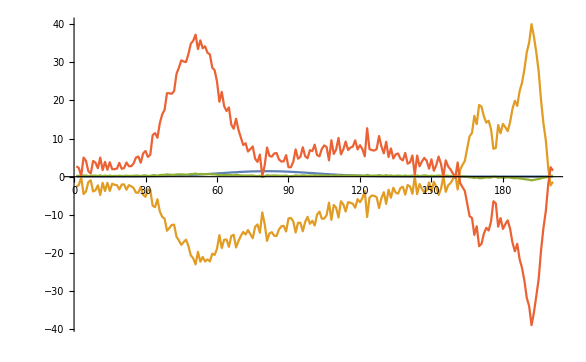

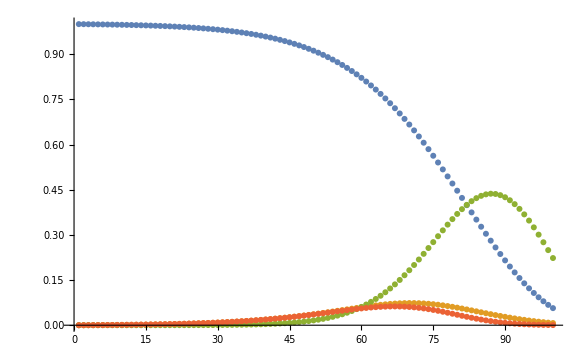

```mathematica
sas = Transpose[tominimizetargetta[kresults,times,data,True]];
components = Transpose[Table[{solutiona[kresults[[1]],kresults[[2]],kresults[[3]],kresults[[4]],kresults[[5]],t],solutionb[kresults[[1]],kresults[[2]],kresults[[3]],kresults[[4]],kresults[[5]],t],solutionc[kresults[[1]],kresults[[2]],kresults[[3]],kresults[[4]],kresults[[5]],t],
solutiond[kresults[[1]],kresults[[2]],kresults[[3]],kresults[[4]],kresults[[5]],t]},{t,Flatten[times]}]];

ListPlot[{sas[[1]],sas[[2]],sas[[3]],sas[[4]]},Joined->True,PlotRange->All]
ListPlot[{components[[1]],components[[2]],components[[3]],components[[4]]}]
```

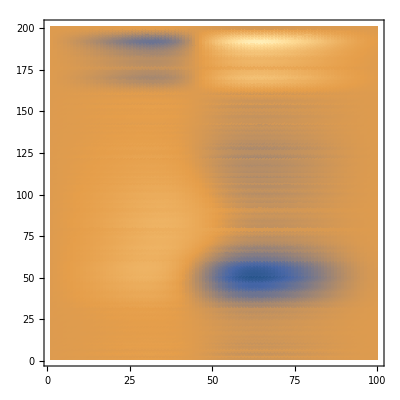

```mathematica
ListDensityPlot[residue,PlotRange->All]
```

```mathematica
Export["./global_analysis/linear_spectra_wrong_model.csv",{Flatten[wavelengths],sas[[1]],sas[[2]],sas[[3]],sas[[4]]}]
Export["./global_analysis/linear_components_wrong_model.csv",{Flatten[times],components[[1]],components[[2]],components[[3]],components[[4]]}]
```

./global_analysis/linear_spectra_wrong_model.csv

./global_analysis/linear_components_wrong_model.csv

CA for Branch Species Dataset

```mathematica
(* ----- SVD Analysis ---- *)  

(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ branchdata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0branch(* time to start fitting fs*), t1branch (* time to end fitting (fs) *) ,"No Flip"];
```

```mathematica
(* choose eqyation *) 

t0 = times[[1,1]];
t1 = times[[-1,1]] ;

ClearAll[k1,k2,k3,k4];

sol=ParametricNDSolveValue[{
D[a[t],t]==-k1*a[t],
a[t0] == 1,
D[b[t],t]==k1*a[t]-k2*b[t],
b[t0] == 0,
D[c[t],t]==k2*b[t]-k3 *c[t],
c[t0] == 0,
D[d[t],t]==k2*b[t]-k4 *d[t],
d[t0] == 0},
{a,b,c,d},{t,t0,t1},{k1,k2,k3,k4}];


(*functions for selecting parts of the solution*)
solutiona[k1_,k2_,k3_,k4_,t_]:=Module[{},asol=sol[k1,k2,k3,k4][[1]][t];
Return[asol]]

solutionb[k1_,k2_,k3_,k4_,t_]:=Module[{},bsol=sol[k1,k2,k3,k4][[2]][t];
Return[bsol]]

solutionc[k1_,k2_,k3_,k4_,t_]:=Module[{},csol=sol[k1,k2,k3,k4][[3]][t];
Return[csol]]

solutiond[k1_,k2_,k3_,k4_,t_]:=Module[{},dsol=sol[k1,k2,k3,k4][[4]][t];
Return[dsol]]


ClearAll[k1,k2,k3,k4];
```

```mathematica
tominimizetargetta[taus_?(VectorQ[#,NumericQ]&),times_,data_,export_]:=Block[{kineticsmatrix,matrixD,matrixDAS,residue,matrixs,toreduce}, 
kineticsmatrix = Transpose[Table[{solutiona[taus[[1]],taus[[2]],taus[[3]],taus[[4]],t],solutionb[taus[[1]],taus[[2]],taus[[3]],taus[[4]],t],solutionc[taus[[1]],taus[[2]],taus[[3]],taus[[4]],t],solutiond[taus[[1]],taus[[2]],taus[[3]],taus[[4]],t]},{t,Flatten[times]}]];
matrixs= Transpose[data].PseudoInverse[kineticsmatrix];
toreduce = Transpose[data]-matrixs.kineticsmatrix;
residue = Total[(toreduce)^2,2];
If[export==False, 
Return[residue];, 
Return[matrixs]];
]
```

```mathematica
taus = {1/8,1/30,1/500,1/1000};
limits = {{1/10,1/5},{1/100,1/50},{1/1000,1/400},{1/2000,1/800}};

(* you must give the same number of taus as selectedvectors *) 
If[Length[taus]==4,
, 
Interrupt[];
]
 
(* limits of lifetimes *) 
variables=Table[t[i],{i,Length[taus]}];
f[{min_,max_},{pos_}]:=min<t[pos]<max
region=And@@MapIndexed[f,limits];
```

```mathematica
values1={};
Monitor[minfit=FindMinimum[{tominimizetargetta[variables,times,data,False],region},variables,Method->"Automatic",
EvaluationMonitor:>(AppendTo[values1,{variables[[1]],variables[[2]],variables[[3]],variables[[4]],tominimizetargetta[variables,times,data,False]}];)], Quiet@ListLogLinearPlot[{values1[[-200;;,{1,-1}]],values1[[-200;;,{2,-1}]],values1[[-200;;,{3,-1}]]},Joined->True]]
```

{23.6205,{t[1]→0.154064,t[2]→0.02,t[3]→0.0025,t[4]→0.000604402}}

```mathematica
kresults = {minfit[[2,1,2]],minfit[[2,2,2]],minfit[[2,3,2]],minfit[[2,4,2]]}
```

{0.154064,0.02,0.0025,0.000604402}

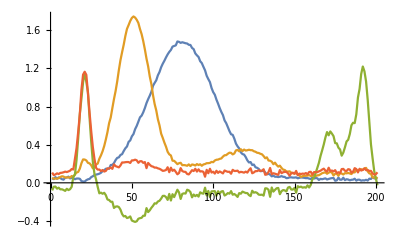

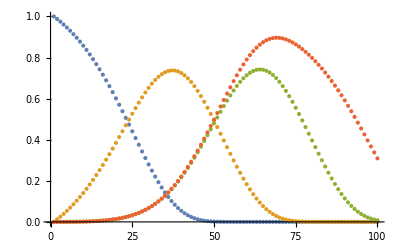

```mathematica
sas = Transpose[tominimizetargetta[kresults,times,data,True]];
components = Transpose[Table[{solutiona[kresults[[1]],kresults[[2]],kresults[[3]],kresults[[4]],t],solutionb[kresults[[1]],kresults[[2]],kresults[[3]],kresults[[4]],t],solutionc[kresults[[1]],kresults[[2]],kresults[[3]],kresults[[4]],t],solutiond[kresults[[1]],kresults[[2]],kresults[[3]],kresults[[4]],t]},{t,Flatten[times]}]];

ListPlot[{sas[[1]],sas[[2]],sas[[3]],sas[[4]]},Joined->True,PlotRange->All]
ListPlot[{components[[1]],components[[2]],components[[3]],components[[4]]}]
```

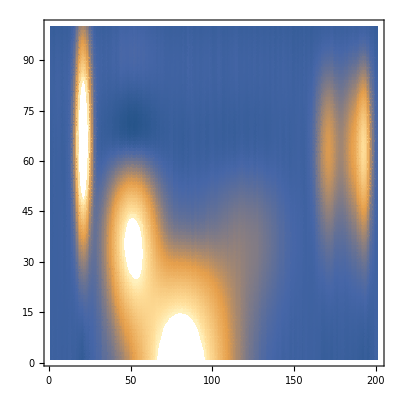

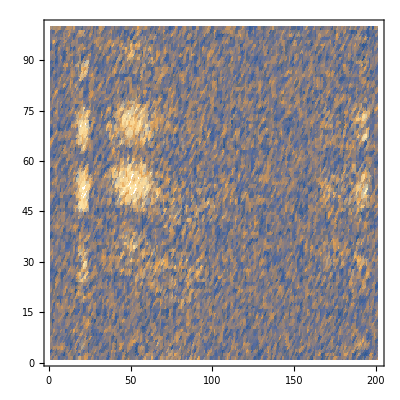

```mathematica
ListDensityPlot[Transpose[components].sas]
ListDensityPlot[Abs[data-Transpose[components].sas]]
```

```mathematica
Export["./global_analysis/branches_spectrum.csv",{Flatten[wavelengths],sas[[1]],sas[[2]],sas[[3]],sas[[4]]}];
Export["./global_analysis/branches_kinetic.csv",{Flatten[times],components[[1]],components[[2]],components[[3]],components[[4]]}];
```

## Known Spectra

```mathematica
tominimizetargetta[taus_?(VectorQ[#,NumericQ]&),times_,data_,export_]:=Block[{kineticsmatrix,matrixD,matrixDAS,residue,matrixs,toreduce}, 
kineticsmatrix = Transpose[Table[{solutiona[taus[[1]],taus[[2]],taus[[3]],t],solutionb[taus[[1]],taus[[2]],taus[[3]],t],solutionc[taus[[1]],taus[[2]],taus[[3]],t]},{t,Flatten[times]}]];
matrixs= Transpose[data].PseudoInverse[kineticsmatrix];
toreduce = Transpose[data]-matrixs.kineticsmatrix;
residue = Total[(toreduce)^2,2];
If[export==False, 
Return[residue];, 
Return[matrixs]];
]
```

CA for Moving Species Dataset

```mathematica
(* ----- Choose Data ---- *)  

(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ movingdata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0species(* time to start fitting fs*), t1species (* time to end fitting (fs) *) ,"No Flip"];
```

```mathematica
(* choose eqyation *) 

t0 = times[[1,1]];
t1 = times[[-1,1]] ;

ClearAll[k1,k2,k3];

(* add additional wavelength dependence *) 
sol=ParametricNDSolveValue[{
D[a[t],t]==-k1*a[t]-k2*a[t]-k3*a[t],
a[t0] == 1},
{a},{t,t0,t1},{k1,k2,k3}];


spectrum1[w_,t_,spread_,centre_] := Module[{v},
v= PDF[NormalDistribution[650+t/centre,20+t/spread]][w];
Return[50*v];
];


(*functions for selecting parts of the solution*)
solutiona[k1_,k2_,k3_,t_]:=Module[{},asol=sol[k1,k2,k3][[1]][t];
Return[asol]]
```

```mathematica
Clear[tominimizetarget]
tominimizetarget[taus_?(VectorQ[#,NumericQ]&),data_,times_,wavelengths_]:=Block[{matrixD,matrixDAS,residue}, 
matrixD = N[Table[solutiona[taus[[1]],taus[[2]],taus[[3]],t]*spectrum1[Flatten[wavelengths],t,taus[[4]],taus[[5]]],{t,Flatten[times]}]];
residue = Total[(data - matrixD)^2,2];
Return[residue];
]
```

```mathematica
taus = {1/2000,1/800,1/1000,150,15};
limits = {{1/2500,1/2000},{1/1000,1/500},{1/1200,1/900},{140,160},{14,16}};

(* you must give the same number of taus as selectedvectors *) 
If[Length[taus]==5,
, 
Interrupt[];
]
 
(* limits of lifetimes *) 
variables=Table[t[i],{i,Length[taus]}];
f[{min_,max_},{pos_}]:=min<t[pos]<max
region=And@@MapIndexed[f,limits];
```

```mathematica
values1={};
Monitor[minfit=FindMinimum[{tominimizetarget[variables,data,times,wavelengths],region},variables,Method->"Automatic",
EvaluationMonitor:>(AppendTo[values1,{variables[[1]],variables[[2]],variables[[3]],variables[[4]],tominimizetarget[variables,data,times,wavelengths]}];)], Quiet@ListLogLinearPlot[{values1[[-200;;,{1,-1}]],values1[[-200;;,{2,-1}]],values1[[-200;;,{3,-1}]]},Joined->True]]
```

{115.789,{t[1]→0.0004,t[2]→0.001,t[3]→0.000833333,t[4]→140.,t[5]→15.0146}}

```mathematica
kresults = {minfit[[2,1,2]],minfit[[2,2,2]],minfit[[2,3,2]],minfit[[2,4,2]],minfit[[2,5,2]]}
```

{0.0004,0.001,0.000833333,140.,15.0146}

```mathematica
output = N[Table[solutiona[kresults[[1]],kresults[[2]],kresults[[3]],t]*spectrum1[Flatten[wavelengths],t,kresults[[4]],kresults[[5]]],{t,Flatten[times]}]];
componenta = Table[solutiona[kresults[[1]],kresults[[2]],kresults[[3]],t],{t,Flatten[times]}];
ListDensityPlot[data-output]
```

-Graphics-

```mathematica
Export["./global_analysis/moving_spectrum.csv",{Flatten[wavelengths],spectrum1[Flatten[wavelengths],0,kresults[[4]],kresults[[5]]],spectrum1[Flatten[wavelengths],100,kresults[[4]],kresults[[5]]],spectrum1[Flatten[wavelengths],500,kresults[[4]],kresults[[5]]]}];
Export["./global_analysis/moving_kinetic.csv",{Flatten[times],componenta}];
```

SVD -> GA for Individual Species Dataset, 3 lifetimes

```mathematica
(* ----- SVD Analysis ---- *)  
(* SVD analysis used as known spectra - arbitrary ones can be used *) 
(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ speciesdata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0species(* time to start fitting fs*), t1species (* time to end fitting (fs) *) ,"No Flip"];

Dimensions[data]
(* take SVD decomposition to investigate which bases to keep *) 
{matrixU,matrixS,wLSV,matrixV} = svd[data];

(* time and wavelength reduced dataset *) 
ListDensityPlot[data,PlotRange->All]

numberofbasis = 10; (* must be less than dimensions of x *) 
basis=Transpose[{Flatten[times],Flatten[wLSV[[;;,{#}]]]}]&/@ Range[numberofbasis];

Manipulate[GraphicsRow[{ListPlot[basis[[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Time [fs]","wLSV "<>ToString[i]}}],ListPlot[Transpose[matrixV][[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Wavelength","wLSV "<>ToString[i]}}]}],{i,1,numberofbasis,1}]

(* From the Manipulate, select which vectors you wish to keep *) 
selectedvectors = {1,2,3};
```

```mathematica
(* choose eqyation *) 

t0 = times[[1,1]];
t1 = times[[-1,1]] ;

ClearAll[k1,k2,k3];
sol=ParametricNDSolveValue[{
D[a[t],t]==-k1*a[t],
a[t0] == 1,
D[b[t],t]==k1*a[t]-k2*b[t],
b[t0] == 0,
D[c[t],t]==k2*b[t]-k3 c[t],
c[t0] == 0},
{a,b,c},{t,t0,t1},{k1,k2,k3}]

(*functions for selecting parts of the solution*)
solutiona[k1_,k2_,k3_,t_]:=Module[{},asol=sol[k1,k2,k3][[1]][t];
Return[asol]]

solutionb[k1_,k2_,k3_,t_]:=Module[{},bsol=sol[k1,k2,k3][[2]][t];
Return[bsol]]

solutionc[k1_,k2_,k3_,t_]:=Module[{},csol=sol[k1,k2,k3][[3]][t];
Return[csol]]

ClearAll[k1,k2,k3,kdcbq];
```

```mathematica
Clear[tominimizetarget]
tominimizetarget[taus_?(VectorQ[#,NumericQ]&),matrixY_,times_]:=Block[{matrixD,matrixDAS,residue}, 
matrixD = Table[{solutiona[taus[[1]],taus[[2]],taus[[3]],t],solutionb[taus[[1]],taus[[2]],taus[[3]],t],solutionc[taus[[1]],taus[[2]],taus[[3]],t]},{t,Flatten[times]}];
matrixDAS=LeastSquares[matrixD,matrixY];
residue = Total[(matrixY - matrixD.matrixDAS)^2,2];
Return[residue];
]
```

```mathematica
wLSVreduced = wLSV[[;;,selectedvectors]];

(* lets guess our lifetimes - must match number of wLSV*) 
taus = {1/10,1/30,1/200};
limits = {{1/1000,1/2},{1/10000,1/10},{1/10000,1/10}};

(* you must give the same number of taus as selectedvectors *) 
If[Length[taus]==Length[selectedvectors],
, 
Interrupt[];
]
 
(* limits of lifetimes *) 
variables=Table[t[i],{i,Length[taus]}];
f[{min_,max_},{pos_}]:=min<t[pos]<max
region=And@@MapIndexed[f,limits];

(* generate D *) 
matrixD = Table[{solutiona[taus[[1]],taus[[2]],taus[[3]],t],solutionb[taus[[1]],taus[[2]],taus[[3]],t],solutionc[taus[[1]],taus[[2]],taus[[3]],t]},{t,Flatten[times]}];

(* generate Decay Associated Spectra *) 
matrixDAS=LeastSquares[matrixD,wLSVreduced];

values1={}; 
(* run minimisation algorithim *) 
Monitor[minfit=FindMinimum[{tominimizetarget[variables,wLSVreduced,times],region},variables,Method->"Automatic",
EvaluationMonitor:>(AppendTo[values1,{variables[[1]],variables[[2]],variables[[3]],tominimizetarget[variables,wLSVreduced,times]}];)], Quiet@ListLogLinearPlot[{values1[[-200;;,{1,4}]],values1[[-200;;,{2,4}]],values1[[-200;;,{3,4}]]},Joined->True]]
```

```mathematica
(* ------ Quality of Fit ------- *) 

values1=SortBy[values1,#[[4]]&];
{k1,k2,k3}=values1[[1]][[1;;3]];
{k1,k2,k3}^(-1)
concentrations = Table[{solutiona[k1,k2,k3,t],solutionb[k1,k2,k3,t],solutionc[k1,k2,k3,t]},{t,Flatten[times]}];
```

```mathematica
matrixD = Table[{solutiona[k1,k2,k3,t],solutionb[k1,k2,k3,t],solutionc[k1,k2,k3,t]},{t,Flatten[times]}];
matrixDAS=LeastSquares[matrixD,wLSVreduced]

result1 = Transpose[{Flatten[times],#}]&/@Transpose[matrixD.matrixDAS];
result2 = Transpose[{Flatten[times],#}]&/@Transpose[wLSVreduced];

Show[ListPlot[result1,Joined->True,PlotRange->All],ListPlot[result2,PlotRange->All]]

Show[ListPlot3D[{data,matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]},PlotRange->All]]

result3= Transpose[{Flatten[times],#}]&/@Transpose[matrixD];
ListPlot[result3]

residues = Abs[data-matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]];
ListPlot3D[residues,PlotRange-> All];
```

SVD -> GA for Individual Species Dataset, 9 lifetimes

```mathematica
(* ----- SVD Analysis ---- *)  

(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ speciesdata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0species(* time to start fitting fs*), t1species (* time to end fitting (fs) *) ,"No Flip"];

Dimensions[data]
(* take SVD decomposition to investigate which bases to keep *) 
{matrixU,matrixS,wLSV,matrixV} = svd[data];

(* time and wavelength reduced dataset *) 
ListDensityPlot[data,PlotRange->All]

numberofbasis = 10; (* must be less than dimensions of x *) 
basis=Transpose[{Flatten[times],Flatten[wLSV[[;;,{#}]]]}]&/@ Range[numberofbasis];

Manipulate[GraphicsRow[{ListPlot[basis[[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Time [fs]","wLSV "<>ToString[i]}}],ListPlot[Transpose[matrixV][[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Wavelength","wLSV "<>ToString[i]}}]}],{i,1,numberofbasis,1}]

(* From the Manipulate, select which vectors you wish to keep *) 
selectedvectors = {1,2,3};
```

```mathematica
(* choose eqyation *) 

t0 = times[[1,1]];
t1 = times[[-1,1]] ;

ClearAll[k1,k2,k3];
(* write out and solve our differential equation *) 
sol=ParametricNDSolveValue[{
D[a[t],t]==-k11*a[t]-k12*a[t]-k13*a[t],
a[t0] == 1,
D[b[t],t]==k11*a[t]+k12*a[t]+k13*a[t]-k21*b[t]-k22*b[t]-k23*b[t],
b[t0] == 0,
D[c[t],t]==k21*b[t]+k22*b[t]+k23*b[t]-k31 *c[t]-k32*c[t]-k33* c[t],
c[t0] == 0},
{a,b,c},{t,t0,t1},{k11,k12,k13,k21,k22,k23,k31,k32,k33}];


(*functions for selecting parts of the solution*)
solutiona[k11_,k12_,k13_,k21_,k22_,k23_,k31_,k32_,k33_,t_]:=Module[{},asol=sol[k11,k12,k13,k21,k22,k23,k31,k32,k33][[1]][t];
Return[asol]]

solutionb[k11_,k12_,k13_,k21_,k22_,k23_,k31_,k32_,k33_,t_]:=Module[{},bsol=sol[k11,k12,k13,k21,k22,k23,k31,k32,k33][[2]][t];
Return[bsol]]

solutionc[k11_,k12_,k13_,k21_,k22_,k23_,k31_,k32_,k33_,t_]:=Module[{},csol=sol[k11,k12,k13,k21,k22,k23,k31,k32,k33][[3]][t];
Return[csol]]

ClearAll[k1,k2,k3,kdcbq];
```

```mathematica
Clear[tominimizetarget]
tominimizetarget[taus_?(VectorQ[#,NumericQ]&),matrixY_,times_]:=Block[{matrixD,matrixDAS,residue}, 
matrixD = Table[{solutiona[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],taus[[7]],taus[[8]],taus[[9]],t],solutionb[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],taus[[7]],taus[[8]],taus[[9]],t],solutionc[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],taus[[7]],taus[[8]],taus[[9]],t]},{t,Flatten[times]}];
matrixDAS=LeastSquares[matrixD,matrixY];
residue = Total[(matrixY - matrixD.matrixDAS)^2,2];
Return[residue];
]
```

```mathematica
wLSVreduced = wLSV[[;;,selectedvectors]];

(* lets guess our lifetimes - must match number of wLSV*) 
taus =  { 1/8,1/20, 1/50, 1/30, 1/60,1/100, 1/500,1/1000, 1/2000};
limits = {{1/10000,1/10},{1/10000,1/10},{1/10000,1/10},{1/10000,1/10},{1/10000,1/10},{1/10000,1/10},{1/10000,1/10},{1/10000,1/10},{1/10000,1/10}};

 
(* limits of lifetimes *) 
variables=Table[t[i],{i,Length[taus]}];
f[{min_,max_},{pos_}]:=min<t[pos]<max
region=And@@MapIndexed[f,limits];

(* generate D *) 
matrixD = Table[{solutiona[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],taus[[7]],taus[[8]],taus[[9]],t],solutionb[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],taus[[7]],taus[[8]],taus[[9]],t],solutionc[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],taus[[7]],taus[[8]],taus[[9]],t]},{t,Flatten[times]}];

(* generate Decay Associated Spectra *) 
matrixDAS=LeastSquares[matrixD,wLSVreduced];

values1={}; 
(* run minimisation algorithim *) 
minfit=FindMinimum[{tominimizetarget[variables,wLSVreduced,times],region},variables,Method->"Automatic",
EvaluationMonitor:>(AppendTo[values1,{variables[[1]],variables[[2]],variables[[3]],variables[[4]],variables[[5]],variables[[6]],variables[[7]],variables[[8]],variables[[9]],tominimizetarget[variables,wLSVreduced,times]}];)]
```

```mathematica
(* ------ Quality of Fit ------- *) 

values1=SortBy[values1,#[[-1]]&];
{k11,k12,k13,k21,k22,k23,k31,k32,k33}=values1[[1]][[1;;9]];
{k11,k12,k13,k21,k22,k23,k31,k32,k33}^(-1)
concentrations = Table[{solutiona[k11,k12,k13,k21,k22,k23,k31,k32,k33,t],solutionb[k11,k12,k13,k21,k22,k23,k31,k32,k33,t],solutionc[k11,k12,k13,k21,k22,k23,k31,k32,k33,t]},{t,Flatten[times]}];
```

```mathematica
matrixD = Table[{solutiona[k11,k12,k13,k21,k22,k23,k31,k32,k33,t],solutionb[k11,k12,k13,k21,k22,k23,k31,k32,k33,t],solutionc[k11,k12,k13,k21,k22,k23,k31,k32,k33,t]},{t,Flatten[times]}];
matrixDAS=LeastSquares[matrixD,wLSVreduced]

result1 = Transpose[{Flatten[times],#}]&/@Transpose[matrixD.matrixDAS];
result2 = Transpose[{Flatten[times],#}]&/@Transpose[wLSVreduced];

Show[ListPlot[result1,Joined->True,PlotRange->All],ListPlot[result2,PlotRange->All]]

Show[ListPlot3D[{data,matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]},PlotRange->All]]

result3= Transpose[{Flatten[times],#}]&/@Transpose[matrixD];
ListPlot[result3]

residues = Abs[data-matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]];
ListPlot3D[residues,PlotRange-> All];
```

SVD -> GA TA for “Complicated” Dataset

```mathematica
(* ----- SVD Analysis ---- *)  

(* select datarange we are interested in *) 
{data,ntimes,nwavelengths,times,wavelengths} =selectdata[ complicateddata (* dataset*) , 600 (* lower wavelength *) , 800 (* upper wavelength*) ,t0species(* time to start fitting fs*), t1species (* time to end fitting (fs) *) ,"No Flip"];

Dimensions[data]
(* take SVD decomposition to investigate which bases to keep *) 
{matrixU,matrixS,wLSV,matrixV} = svd[data];

(* time and wavelength reduced dataset *) 
ListDensityPlot[data,PlotRange->All]

numberofbasis = 10; (* must be less than dimensions of x *) 
basis=Transpose[{Flatten[times],Flatten[wLSV[[;;,{#}]]]}]&/@ Range[numberofbasis];

Manipulate[GraphicsRow[{ListPlot[basis[[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Time [fs]","wLSV "<>ToString[i]}}],ListPlot[Transpose[matrixV][[i]],Joined->True,Frame->True,FrameLabel->{{"Contribution"," "},{"Wavelength","wLSV "<>ToString[i]}}]}],{i,1,numberofbasis,1}]

(* From the Manipulate, select which vectors you wish to keep *) 
selectedvectors = {1,2,3,4};
```

```mathematica
(* choose eqyation *) 

t0 = times[[1,1]];
t1 = times[[-1,1]] ;

ClearAll[k11,k12,k21,k31,k32,k41]
(* write out and solve our differential equation *) 
sol=ParametricNDSolveValue[{
D[a[t],t]==-k11*a[t]-k12*a[t],
a[t0] == 1,
D[b[t],t]==k11*a[t]-k21*b[t]+k41*d[t],
b[t0] == 0,
D[c[t],t]==k12*a[t] - k31*c[t]-k32*c[t],
c[t0] == 0,
D[d[t],t]==k21*b[t]-k41*d[t],
d[t0] == 0,
D[e[t],t]==k32*c[t],
e[t0] == 0},
{a,b,c,d,e},{t,t0,t1},{k11,k12,k21,k31,k32,k41}];


(*functions for selecting parts of the solution*)
solutiona[k11_,k12_,k21_,k31_,k32_,k41_,t_]:=Module[{},asol=sol[k11,k12,k21,k31,k32,k41][[1]][t];
Return[asol]]

solutionb[k11_,k12_,k21_,k31_,k32_,k41_,t_]:=Module[{},bsol=sol[k11,k12,k21,k31,k32,k41][[2]][t];
Return[bsol]]

solutionc[k11_,k12_,k21_,k31_,k32_,k41_,t_]:=Module[{},csol=sol[k11,k12,k21,k31,k32,k41][[3]][t];
Return[csol]]

solutiond[k11_,k12_,k21_,k31_,k32_,k41_,t_]:=Module[{},dsol=sol[k11,k12,k21,k31,k32,k41][[4]][t];
Return[dsol]]

solutione[k11_,k12_,k21_,k31_,k32_,k41_,t_]:=Module[{},esol=sol[k11,k12,k21,k31,k32,k41][[5]][t];
Return[esol]]
```

```mathematica
Clear[tominimizetarget]
tominimizetarget[taus_?(VectorQ[#,NumericQ]&),matrixY_,times_]:=Block[{matrixD,matrixDAS,residue}, 
matrixD = Table[{solutiona[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],t],solutionb[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],t],solutionc[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],t],solutiond[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],t],solutione[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],t]},{t,Flatten[times]}];
matrixDAS=LeastSquares[matrixD,matrixY];
residue = Total[(matrixY - matrixD.matrixDAS)^2,2];
Return[residue];
]
```

```mathematica
wLSVreduced = wLSV[[;;,selectedvectors]];

(* lets guess our lifetimes - must match number of wLSV*) 
taus =  { 1/8,1/5, 1/100, 1/200, 1/400,1/120};
limits = {{1/12,1/7},{1/6,1/4},{1/120,1/80},{1/220,1/190},{1/410,1/390},{1/140,1/100}};

 
(* limits of lifetimes *) 
variables=Table[t[i],{i,Length[taus]}];
f[{min_,max_},{pos_}]:=min<t[pos]<max
region=And@@MapIndexed[f,limits];

(* generate D *) 
matrixD = Table[{solutiona[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]]t],solutionb[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],t],solutionc[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],t],solutiond[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],t],solutione[taus[[1]],taus[[2]],taus[[3]],taus[[4]],taus[[5]],taus[[6]],t]},{t,Flatten[times]}];

(* generate Decay Associated Spectra *) 
matrixDAS=LeastSquares[matrixD,wLSVreduced];

values1={}; 
(* run minimisation algorithim *) 
minfit=FindMinimum[{tominimizetarget[variables,wLSVreduced,times],region},variables,Method->"Automatic",
EvaluationMonitor:>(AppendTo[values1,{variables[[1]],variables[[2]],variables[[3]],variables[[4]],variables[[5]],variables[[6]],tominimizetarget[variables,wLSVreduced,times]}];)]
```

```mathematica
(* ------ Quality of Fit ------- *) 

values1=SortBy[values1,#[[-1]]&];
{k11,k12,k21,k31,k32,k41}=values1[[1]][[1;;6]]
{k11,k12,k21,k31,k32,k41}^(-1);
concentrations = Table[{solutiona[k11,k12,k21,k31,k32,k41,t],solutionb[k11,k12,k21,k31,k32,k41,t],solutionc[k11,k12,k21,k31,k32,k41,t]},{t,Flatten[times]}];
```

```mathematica
concentrations = Table[{solutiona[1/8,1/5, 1/100, 1/200, 1/400,1/120,t],solutionb[1/8,1/5, 1/100, 1/200, 1/400,1/120,t],solutionc[1/8,1/5, 1/100, 1/200, 1/400,1/120,t]},{t,Flatten[times]}];

matrixD = Table[{solutiona[1/8,1/5, 1/100, 1/200, 1/400,1/120,t],solutionb[1/8,1/5, 1/100, 1/200, 1/400,1/120,t],solutionc[1/8,1/5, 1/100, 1/200, 1/400,1/120,t],solutiond[1/8,1/5, 1/100, 1/200, 1/400,1/120,t]},{t,Flatten[times]}];
matrixDAS=LeastSquares[matrixD,wLSVreduced]

result1 = Transpose[{Flatten[times],#}]&/@Transpose[matrixD.matrixDAS];
result2 = Transpose[{Flatten[times],#}]&/@Transpose[wLSVreduced];

Show[ListPlot[result1,Joined->True,PlotRange->All],ListPlot[result2,PlotRange->All]]

Show[ListPlot3D[{data,matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]},PlotRange->All]]

result3= Transpose[{Flatten[times],#}]&/@Transpose[matrixD];
ListPlot[result3]

residues = Abs[data-matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]];
ListPlot3D[residues,PlotRange-> All];
```

```mathematica
matrixD = Table[{solutiona[k11,k12,k21,k31,k32,k41,t],solutionb[k11,k12,k21,k31,k32,k41,t],solutionc[k11,k12,k21,k31,k32,k41,t],solutiond[k11,k12,k21,k31,k32,k41,t],solutione[k11,k12,k21,k31,k32,k41,t]},{t,Flatten[times]}];
matrixDAS=LeastSquares[matrixD,wLSVreduced]

result1 = Transpose[{Flatten[times],#}]&/@Transpose[matrixD.matrixDAS];
result2 = Transpose[{Flatten[times],#}]&/@Transpose[wLSVreduced];

Show[ListPlot[result1,Joined->True,PlotRange->All],ListPlot[result2,PlotRange->All]]

Show[ListPlot3D[{data,matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]},PlotRange->All]]

result3= Transpose[{Flatten[times],#}]&/@Transpose[matrixD];
ListPlot[result3]

residues = Abs[data-matrixD.matrixDAS.Transpose[matrixV[[;;,selectedvectors]]]];
ListPlot3D[residues,PlotRange-> All];
```

```mathematica
(* generate design matrix *) 
generateD2[times_,taus_]:=Block[{matrixD,timesnum,i,j,numtau},
timesnum=Length[times]; 
numtau=Length[taus];
matrixD = Quiet[Table[SetPrecision[Exp[-times[[i]]/taus[[j]]],10],{i,1,timesnum,1},{j,1,numtau,1}]];
matrixD=Flatten[#]&/@matrixD;
Return[matrixD];
];

Clear[tominimize]
tominimize2[taus_?(VectorQ[#,NumericQ]&),matrixY_,times_]:=Block[{matrixD,matrixDAS,residue}, 
matrixD = generateD2[times,taus];
matrixDAS=LeastSquares[matrixD,matrixY];
residue = Total[(matrixY - matrixD.matrixDAS)^2,2];
Return[residue];
]
```

```mathematica
(* Test for DADS other way around *)
```

```mathematica
(* global analysis *)
```

```mathematica
selectedvectors = {1,2,3};
wLSVreduced = wLSV[[;;,selectedvectors]];

(* lets guess our rates - must match number of wLSV*) 
taus = {100,200,300};
limits = {{5,5000},{1,1000},{1,1000}};
 
(* limits of lifetimes *) 
variables=Table[t[i],{i,Length[taus]}];
f[{min_,max_},{pos_}]:=min<t[pos]<max
region=And@@MapIndexed[f,limits];

(* generate D *) 
matrixD = generateD2[Flatten[times],taus];

(* generate Decay Associated Spectra *) 
matrixDAS=LeastSquares[matrixD,wLSVreduced];

(* run minimisation algorithim *) 
nmresults=NMinimize[{tominimize2[variables,wLSVreduced,times],region},variables,PrecisionGoal->10,Method->"SimulatedAnnealing"]
```

```mathematica
ListPlot[Transpose[matrixD.matrixDAS]]
```

```mathematica
(* proper global analysis *) 

spectralcomponents = Transpose[data].PseudoInverse[Transpose[matrixD]];
ListPlot[Transpose[spectralcomponents]]
datanew = spectralcomponents.Transpose[matrixD];

ListDensityPlot[Transpose[data]-datanew]
```

```mathematica
Dimensions[data]
Dimensions[datanew]
```

## Monte-Carlo

## Machine Learning